```mathematica
SetDirectory[NotebookDirectory[]];
```

### Introduction & setup

#### Preliminaries: data structures and constraints

Define number of observables per system and number of outputs of each observable.

```mathematica
observablesCount = {2,2};
valuesCount = {2,2};
```

i.e. we have two subsystems each with two observables and each of these observable have two outputs. Now we set auxilliary variables

```mathematica
totalObservables= Fold[Times,1,observablesCount]
totalValues = Fold[Times, 1, valuesCount]
cumulativeObservablesCount= With[{roc = Reverse[Rest[observablesCount]]}, Reverse[FoldList[Times,1,roc]]]
cumulativeValuesCount= 
With[{rvc = Reverse[Rest[valuesCount]]}, Reverse[FoldList[Times,1,rvc]]]
```

4

4

{2,1}

{2,1}

Finially we make two auxilliary lists that contain all joint basic observables and joint outputs.

```mathematica
jointObservables =listJoint[observablesCount]
jointValues = listJoint[valuesCount]
listJoint[l_]:=Flatten[Outer[List,Sequence@@#]&[Range[#]&/@l],Length[l]-1]
```

listJoint[{2,2}]

listJoint[{2,2}]

Auxilliary functions for pretty printing

```mathematica
list2string[l_List]:=StringJoin@@(ToString/@l);
printQ[question[0]]:="0";
printQ[question[1]]:="1";
printQ[q_question]:=("["<>list2string[#[[1]]-1]<>","<>list2string[#[[2]]-1]<>"]"&)[List@@q]
printQ[q_CirclePlus]:=CirclePlus@@(printQ/@List@@q);
printQ[q_qcmpl]:=printQ[Sequence@@q]<>"^C"
```

For example

```mathematica
printQ[question[{1,1},{0,1}]]
```

[00,-10]

Auxilliary function for calculating probabilities

```mathematica
state2matrix[s_state]:=List[Sequence@@s][[1]];
calculateIndex[v_,cc_]:=With[{rv = #-1&/@v},
Plus@@(Thread[Times[rv,cc]])]+1;
observableIndex[q_question]:=calculateIndex[(List@@q)[[1]],cumulativeObservablesCount];
valueIndex[q_question]:=calculateIndex[(List@@q)[[2]],cumulativeValuesCount];
```

Function for calculating probabilities

```mathematica
pr[q_question,s_state,1]:= With[{sm=state2matrix[s]},
sm[[valueIndex[q],observableIndex[q]]]]
pr[question[1],s_]:= 1;
pr[question[0],s_]:=0;
pr[q_question,s_state]:=pr[q,s,1];
pr[q_qcmpl,s_state]:=1-pr[Sequence@@q,s];
pr[q_CirclePlus,s_]:=Plus@@(pr[#,s]&/@List@@q);
```

Functions implementing Box World constraints

Normalization of a state:

```mathematica
normalizationQ[s_state] := And@@(normalizationQ[#,s]&/@jointObservables);
```

Non signaling with respect to i-th subsystem:

```mathematica
nonsignalQ[s_state,i_]:=And@@(Flatten[nonsignalQ[#,s,i]&/@Range[valuesCount[[i]]],1]);
```

And positivity:

```mathematica
positivityQ[s_state]:=And@@(#≥0&/@Flatten[Sequence@@s]);
```

We used following auxilliary functions

```mathematica
normalizationQ[ol_,s_state] := Plus@@(pr[question[ol,{#[[1]],#[[2]]}],s,1]&/@jointValues)==1;nonsignalQ[x_,y_,z_,va_,s_state,1]:=
Plus@@(pr[question[{x,y},{va,#}],s,1]&/@Range[valuesCount[[2]]])==
Plus@@(pr[question[{x,z},{va,#}],s,1]&/@Range[valuesCount[[2]]]);
nonsignalQ[x_,y_,z_,va_,s_state,2]:=
Plus@@(pr[question[{y,x},{#,va}],s,1]&/@Range[valuesCount[[1]]])==
Plus@@(pr[question[{z,x},{#,va}],s,1]&/@Range[valuesCount[[1]]]);
nonsignalQ[va_,s_state,i_]:=nonsignalQ[#[[1]],#[[2]],#[[3]],va,s,i]&/@forallXYZ[1];
forallXYZ[i_]:=Flatten[Outer[Prepend,Subsets[Range[observablesCount[[i]]],{2}],Range[2],1,1],1];
generalState[]:=state[Table[ToExpression["a"<>ToString[i]<>ToString[j]],{i,totalValues},{j,totalObservables}]];
```

Here we have a list of all constraints in Box World One on a general state of the form

```mathematica
generalState[]//state2matrix//MatrixForm
```

(a11 | a12 | a13 | a14
a21 | a22 | a23 | a24
a31 | a32 | a33 | a34
a41 | a42 | a43 | a44)

```mathematica
allowedStateRestr = And[nonsignalQ[generalState[],1],nonsignalQ[generalState[],2],normalizationQ[generalState[]],positivityQ[generalState[]]]
```

a11+a21==a12+a22&&a13+a23==a14+a24&&a31+a41==a32+a42&&a33+a43==a34+a44&&a11+a31==a13+a33&&a12+a32==a14+a34&&a21+a41==a23+a43&&a22+a42==a24+a44&&a11+a21+a31+a41==1&&a12+a22+a32+a42==1&&a13+a23+a33+a43==1&&a14+a24+a34+a44==1&&a11≥0&&a12≥0&&a13≥0&&a14≥0&&a21≥0&&a22≥0&&a23≥0&&a24≥0&&a31≥0&&a32≥0&&a33≥0&&a34≥0&&a41≥0&&a42≥0&&a43≥0&&a44≥0

Here we have only the equation part and calculate rank of coefficients matrix of constraints

```mathematica
restrictedEqs = Join[List@@nonsignalQ[generalState[],1],List@@nonsignalQ[generalState[],2],List@@normalizationQ[generalState[]]];
rankOfRestrictedCoeffArray = MatrixRank[CoefficientArrays[restrictedEqs,Flatten[Sequence@@generalState[]]][[2]]]
```

8

#### Functions that test order

This one checks if supplied question is indeed a question

```mathematica
isQ[q_]:=With[{gs=generalState[]},
MaxValue[Join[{pr[q,gs]}, List@@allowedStateRestr],Flatten[Sequence@@gs]]≤1];
```

For example:

```mathematica
isQ[question[{1,1},{0,0}]]
```

True

```mathematica
isQ[question[{1,1},{0,0}]⊕question[{1,1},{1,1}]]
```

True

```mathematica
isQ[question[{1,1},{0,0}]⊕question[{0,0},{1,1}]]
```

False

Check if two question are equal

```mathematica
isQEqual[q_,r_]:=With[{gs=generalState[]},
If[pr[q,gs]==pr[r,gs]===False, False,MatrixRank[CoefficientArrays[Join[{pr[q,gs]==pr[r,gs]},restrictedEqs],Flatten[Sequence@@gs]][[2]]]==rankOfRestrictedCoeffArray]];
```

We simply check if equality of probabilities for a general state

```mathematica
pr[q,gs]==pr[r,gs];
```

Increases a rank of constraints.

Finally two functions that check an order

```mathematica
isQLess[q_,r_]:=With[{gs=generalState[]},
MaxValue[Join[{pr[q,gs]-pr[r,gs]},List@@allowedStateRestr],Flatten[Sequence@@gs]]≤0];
isQGreater[q_,r_]:=isQLess[r,q];
```

#### Box World One questions

List of atomic questions

```mathematica
rank1questions = Table[question[{i,j},{k,l}], {i,2},{j,2},{k,2},{l,2}]//Flatten;
```

```mathematica
printQ/@rank1questions
```

{[00,00],[00,01],[00,10],[00,11],[01,00],[01,01],[01,10],[01,11],[10,00],[10,01],[10,10],[10,11],[11,00],[11,01],[11,10],[11,11]}

List of two-term sums of atomic questions

```mathematica
rank2questions = DeleteDuplicates[Select[CirclePlus@@#&/@Subsets[rank1questions,{2}],isQ],isQEqual];
```

```mathematica
printQ/@rank2question
```

rank2question

List of three-term sums of atomic questions (in fact we show that are equal to complements of atomic questions)

```mathematica
rank3questionsCP = DeleteDuplicates[Select[CirclePlus@@#&/@Subsets[rank1questions,{3}],isQ],isQEqual];
rank3questions = DeleteDuplicates[Join[qcmpl/@rank1questions,rank3questionsCP],isQEqual];
```

```mathematica
printQ/@rank3questions
```

{[00,00]^C,[00,01]^C,[00,10]^C,[00,11]^C,[01,00]^C,[01,01]^C,[01,10]^C,[01,11]^C,[10,00]^C,[10,01]^C,[10,10]^C,[10,11]^C,[11,00]^C,[11,01]^C,[11,10]^C,[11,11]^C}

So this is a complete list of questions in Box World One

```mathematica
questions = Join[{question[0],question[1]},rank1questions, rank2questions,rank3questions];
```

```mathematica
Length[questions]
```

82

#### Box World One poset structure

First we generate order structre. It will take a while (go and make a coffee if you have slow computer)

```mathematica
questionsGreater = Function[q,{q,Select[questions, isQGreater[#,q]&]}]/@questions;
questionsLess = Function[q,{q,Select[questions, isQLess[#,q]&]}]/@questions;
orthocomplementList = Function[q, {q,Select[questions, isQEqual[#,qcmpl[q]]&][[1]]}]/@ questions;
```

First list contains for each question a list of questions that are greater than that element. Analogously for second list. The last one stores complementary questions.

Now we implement join and meet, i.e. lowest upper bound and greatest lower bound for two questions, and orthocomplement.

```mathematica
join[q_,r_]:=minQuestion[Intersection[greaterThanList[q],greaterThanList[r]]];
meet[q_,r_]:=maxQuestion[Intersection[lessThanList[q],lessThanList[r]]];
orthocmpl[q_]:=Select[orthocomplementList, #[[1]]==q&][[1,2]];
covers[q_]:=minQuestion[Complement[greaterThanList[q],{q}]];
isLess[q_,r_]:=MemberQ[lessThanList[r],q];
isGreater[q_,r_] := isLess[r,q];
```

We used there few auxilliary functions

```mathematica
greaterThanList[q_]:=Select[questionsGreater,#[[1]]==q&][[1,2]];
lessThanList[q_]:=Select[questionsLess,#[[1]]==q&][[1,2]];
reduceToMinElements[l_]:= Intersection@@(Append[Complement[l,greaterThanList[#]],#]&/@l);
minQuestion[l_]:=FixedPoint[reduceToMinElements,l];
reduceToMaxElements[l_]:= Intersection@@(Append[Complement[l,lessThanList[#]],#]&/@l);
maxQuestion[l_]:=FixedPoint[reduceToMaxElements,l];
```

We check if orthocomplement is indeed orthocomplement

```mathematica
And@@(orthocmpl[orthocmpl[#]]==#&/@questions)
```

True

Now we check orthomodularity

```mathematica
And@@(join[ #[[1]],meet[orthocmpl[#[[1]]],#[[2]]][[1]] ][[1]]==#[[2]]&/@Select[Subsets[questions,{2}],less[Sequence@@#]&])
```

True

Now we look for pairs of questions that have non unique joins and meets

```mathematica
nonuniquejoin=Select[Subsets[questions,{2}], Length[join[Sequence@@#]]>1&];
```

```mathematica
nonuniquemeet=Select[Subsets[questions,{2}], Length[meet[Sequence@@#]]>1&];
```

```mathematica
Partition[Function[{a,b},a<>" and "<>b][Sequence@@#]&/@  Map[printQ,nonuniquejoin,{2}],4]//TableForm
```

[00,00] and [11,00] | [00,00] and [11,01] | [00,00] and [11,10] | [00,00] and [11,11]
[00,01] and [11,00] | [00,01] and [11,01] | [00,01] and [11,10] | [00,01] and [11,11]
[00,10] and [11,00] | [00,10] and [11,01] | [00,10] and [11,10] | [00,10] and [11,11]
[00,11] and [11,00] | [00,11] and [11,01] | [00,11] and [11,10] | [00,11] and [11,11]
[01,00] and [10,00] | [01,00] and [10,01] | [01,00] and [10,10] | [01,00] and [10,11]
[01,01] and [10,00] | [01,01] and [10,01] | [01,01] and [10,10] | [01,01] and [10,11]
[01,10] and [10,00] | [01,10] and [10,01] | [01,10] and [10,10] | [01,10] and [10,11]
[01,11] and [10,00] | [01,11] and [10,01] | [01,11] and [10,10] | [01,11] and [10,11]

A graph of our poset (greater up).

```mathematica
poset=Flatten[Function[q,printQ[q]->printQ[#]&/@covers[q]]/@Complement[questions,{questions[[2]]}]];
```

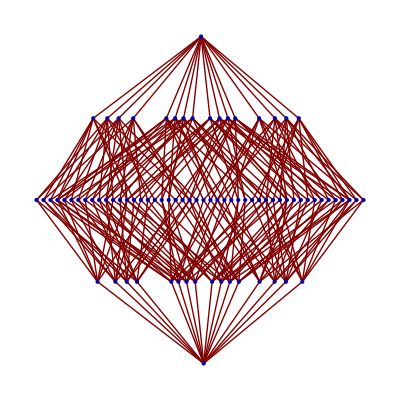

```mathematica
LayeredGraphPlot[poset, Bottom, VertexLabeling->False, DirectedEdges->False, AspectRatio->1.0]
```

```mathematica
covers[questions[[1]]]
```

{question[{1,1},{1,1}],question[{1,1},{1,2}],question[{1,1},{2,1}],question[{1,1},{2,2}],question[{1,2},{1,1}],question[{1,2},{1,2}],question[{1,2},{2,1}],question[{1,2},{2,2}],question[{2,1},{1,1}],question[{2,1},{1,2}],question[{2,1},{2,1}],question[{2,1},{2,2}],question[{2,2},{1,1}],question[{2,2},{1,2}],question[{2,2},{2,1}],question[{2,2},{2,2}]}

```mathematica
{printQ[#],printQ/@covers[#]}&/@questions//Grid
```

Intersection::argm: Intersection called with 0 arguments; 1 or more arguments are expected.

0 | {[00,00],[00,01],[00,10],[00,11],[01,00],[01,01],[01,10],[01,11],[10,00],[10,01],[10,10],[10,11],[11,00],[11,01],[11,10],[11,11]}
1 | Intersection[]
[00,00] | {[00,00]⊕[00,01],[00,00]⊕[00,10],[00,00]⊕[00,11],[00,00]⊕[01,10],[00,00]⊕[01,11],[00,00]⊕[10,01],[00,00]⊕[10,11]}
[00,01] | {[00,00]⊕[00,01],[00,01]⊕[00,10],[00,01]⊕[00,11],[00,01]⊕[01,10],[00,01]⊕[01,11],[00,01]⊕[10,00],[00,01]⊕[10,10]}
[00,10] | {[00,00]⊕[00,10],[00,01]⊕[00,10],[00,10]⊕[00,11],[00,10]⊕[01,00],[00,10]⊕[01,01],[00,10]⊕[10,01],[00,10]⊕[10,11]}
[00,11] | {[00,00]⊕[00,11],[00,01]⊕[00,11],[00,10]⊕[00,11],[00,11]⊕[01,00],[00,11]⊕[01,01],[00,11]⊕[10,00],[00,11]⊕[10,10]}
[01,00] | {[00,00]⊕[00,01],[00,10]⊕[01,00],[00,11]⊕[01,00],[01,00]⊕[01,10],[01,00]⊕[01,11],[01,00]⊕[11,01],[01,00]⊕[11,11]}
[01,01] | {[00,00]⊕[00,01],[00,10]⊕[01,01],[00,11]⊕[01,01],[01,01]⊕[01,10],[01,01]⊕[01,11],[01,01]⊕[11,00],[01,01]⊕[11,10]}
[01,10] | {[00,00]⊕[01,10],[00,01]⊕[01,10],[00,10]⊕[00,11],[01,00]⊕[01,10],[01,01]⊕[01,10],[01,10]⊕[11,01],[01,10]⊕[11,11]}
[01,11] | {[00,00]⊕[01,11],[00,01]⊕[01,11],[00,10]⊕[00,11],[01,00]⊕[01,11],[01,01]⊕[01,11],[01,11]⊕[11,00],[01,11]⊕[11,10]}
[10,00] | {[00,00]⊕[00,10],[00,01]⊕[10,00],[00,11]⊕[10,00],[10,00]⊕[10,01],[10,00]⊕[10,11],[10,00]⊕[11,10],[10,00]⊕[11,11]}
[10,01] | {[00,00]⊕[10,01],[00,01]⊕[00,11],[00,10]⊕[10,01],[10,00]⊕[10,01],[10,01]⊕[10,10],[10,01]⊕[11,10],[10,01]⊕[11,11]}
[10,10] | {[00,00]⊕[00,10],[00,01]⊕[10,10],[00,11]⊕[10,10],[10,01]⊕[10,10],[10,10]⊕[10,11],[10,10]⊕[11,00],[10,10]⊕[11,01]}
[10,11] | {[00,00]⊕[10,11],[00,01]⊕[00,11],[00,10]⊕[10,11],[10,00]⊕[10,11],[10,10]⊕[10,11],[10,11]⊕[11,00],[10,11]⊕[11,01]}
[11,00] | {[01,00]⊕[01,10],[01,01]⊕[11,00],[01,11]⊕[11,00],[10,00]⊕[10,01],[10,10]⊕[11,00],[10,11]⊕[11,00],[11,00]⊕[11,11]}
[11,01] | {[01,00]⊕[11,01],[01,01]⊕[01,11],[01,10]⊕[11,01],[10,00]⊕[10,01],[10,10]⊕[11,01],[10,11]⊕[11,01],[11,01]⊕[11,10]}
[11,10] | {[01,00]⊕[01,10],[01,01]⊕[11,10],[01,11]⊕[11,10],[10,00]⊕[11,10],[10,01]⊕[11,10],[10,10]⊕[10,11],[11,01]⊕[11,10]}
[11,11] | {[01,00]⊕[11,11],[01,01]⊕[01,11],[01,10]⊕[11,11],[10,00]⊕[11,11],[10,01]⊕[11,11],[10,10]⊕[10,11],[11,00]⊕[11,11]}
[00,00]⊕[00,01] | {[00,10]^C,[00,11]^C,[01,10]^C,[01,11]^C}
[00,00]⊕[00,10] | {[00,01]^C,[00,11]^C,[10,01]^C,[10,11]^C}
[00,00]⊕[00,11] | {[00,01]^C,[00,10]^C}
[00,00]⊕[01,10] | {[00,01]^C,[01,11]^C}
[00,00]⊕[01,11] | {[00,01]^C,[01,10]^C}
[00,00]⊕[10,01] | {[00,10]^C,[10,11]^C}
[00,00]⊕[10,11] | {[00,10]^C,[10,01]^C}
[00,01]⊕[00,10] | {[00,00]^C,[00,11]^C}
[00,01]⊕[00,11] | {[00,00]^C,[00,10]^C,[10,00]^C,[10,10]^C}
[00,01]⊕[01,10] | {[00,00]^C,[01,11]^C}
[00,01]⊕[01,11] | {[00,00]^C,[01,10]^C}
[00,01]⊕[10,00] | {[00,11]^C,[10,10]^C}
[00,01]⊕[10,10] | {[00,11]^C,[10,00]^C}
[00,10]⊕[00,11] | {[00,00]^C,[00,01]^C,[01,00]^C,[01,01]^C}
[00,10]⊕[01,00] | {[00,11]^C,[01,01]^C}
[00,10]⊕[01,01] | {[00,11]^C,[01,00]^C}
[00,10]⊕[10,01] | {[00,00]^C,[10,11]^C}
[00,10]⊕[10,11] | {[00,00]^C,[10,01]^C}
[00,11]⊕[01,00] | {[00,10]^C,[01,01]^C}
[00,11]⊕[01,01] | {[00,10]^C,[01,00]^C}
[00,11]⊕[10,00] | {[00,01]^C,[10,10]^C}
[00,11]⊕[10,10] | {[00,01]^C,[10,00]^C}
[01,00]⊕[01,10] | {[01,01]^C,[01,11]^C,[11,01]^C,[11,11]^C}
[01,00]⊕[01,11] | {[01,01]^C,[01,10]^C}
[01,00]⊕[11,01] | {[01,10]^C,[11,11]^C}
[01,00]⊕[11,11] | {[01,10]^C,[11,01]^C}
[01,01]⊕[01,10] | {[01,00]^C,[01,11]^C}
[01,01]⊕[01,11] | {[01,00]^C,[01,10]^C,[11,00]^C,[11,10]^C}
[01,01]⊕[11,00] | {[01,11]^C,[11,10]^C}
[01,01]⊕[11,10] | {[01,11]^C,[11,00]^C}
[01,10]⊕[11,01] | {[01,00]^C,[11,11]^C}
[01,10]⊕[11,11] | {[01,00]^C,[11,01]^C}
[01,11]⊕[11,00] | {[01,01]^C,[11,10]^C}
[01,11]⊕[11,10] | {[01,01]^C,[11,00]^C}
[10,00]⊕[10,01] | {[10,10]^C,[10,11]^C,[11,10]^C,[11,11]^C}
[10,00]⊕[10,11] | {[10,01]^C,[10,10]^C}
[10,00]⊕[11,10] | {[10,01]^C,[11,11]^C}
[10,00]⊕[11,11] | {[10,01]^C,[11,10]^C}
[10,01]⊕[10,10] | {[10,00]^C,[10,11]^C}
[10,01]⊕[11,10] | {[10,00]^C,[11,11]^C}
[10,01]⊕[11,11] | {[10,00]^C,[11,10]^C}
[10,10]⊕[10,11] | {[10,00]^C,[10,01]^C,[11,00]^C,[11,01]^C}
[10,10]⊕[11,00] | {[10,11]^C,[11,01]^C}
[10,10]⊕[11,01] | {[10,11]^C,[11,00]^C}
[10,11]⊕[11,00] | {[10,10]^C,[11,01]^C}
[10,11]⊕[11,01] | {[10,10]^C,[11,00]^C}
[11,00]⊕[11,11] | {[11,01]^C,[11,10]^C}
[11,01]⊕[11,10] | {[11,00]^C,[11,11]^C}
[00,00]^C | {1}
[00,01]^C | {1}
[00,10]^C | {1}
[00,11]^C | {1}
[01,00]^C | {1}
[01,01]^C | {1}
[01,10]^C | {1}
[01,11]^C | {1}
[10,00]^C | {1}
[10,01]^C | {1}
[10,10]^C | {1}
[10,11]^C | {1}
[11,00]^C | {1}
[11,01]^C | {1}
[11,10]^C | {1}
[11,11]^C | {1}

### Various Checks

#### Classicaly correlated boxes

These two functions are used to define classicaly correlated states

```mathematica
classicalStateCoeff[α_,β_,γ_,δ_,question[{x_,y_},{a_,b_}]]:=If[ a-1 == Mod[α x+β-1,2] && b-1 == Mod[γ y+δ-1,2],1,0];classicalState[α_,β_,γ_,δ_]:=generalState[]//.((pr[#,generalState[]]->classicalStateCoeff[α,β,γ,δ,#])&/@rank1questions)
```

We generate the list of 16 extreme classicaly correlated states

```mathematica
classicalStates = classicalState[Sequence@@#]& /@ Tuples[{0,1},4]
```

{state[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,1,1,1}}],state[{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,0,0,0}}],state[{{0,0,0,0},{0,0,0,0},{1,0,1,0},{0,1,0,1}}],state[{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,0,1,0}}],state[{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,0,0,0}}],state[{{1,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}],state[{{1,0,1,0},{0,1,0,1},{0,0,0,0},{0,0,0,0}}],state[{{0,1,0,1},{1,0,1,0},{0,0,0,0},{0,0,0,0}}],state[{{0,0,0,0},{1,1,0,0},{0,0,0,0},{0,0,1,1}}],state[{{1,1,0,0},{0,0,0,0},{0,0,1,1},{0,0,0,0}}],state[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}],state[{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}],state[{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,0,0}}],state[{{0,0,1,1},{0,0,0,0},{1,1,0,0},{0,0,0,0}}],state[{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}],state[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}]}

They look as follows

```mathematica
MatrixForm[Sequence@@#]& /@classicalStates
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0),(0 | 0 | 0 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1),(1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

Just checking if they are indeed non-signalling

```mathematica
nonsignalQ[#,1]&/@classicalStates
nonsignalQ[#,2]&/@classicalStates
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

For the puprpose of question generation we make a list of coefficients that we will use in convex combination, with approprate restrictions.

```mathematica
convexCoeffs = Table[ToExpression["c"<>ToString[i]],{i,16}] 
convexCoeffRestr = Join[{Plus@@convexCoeffs==1},0≤#≤1&/@convexCoeffs]
```

{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16}

{c1+c10+c11+c12+c13+c14+c15+c16+c2+c3+c4+c5+c6+c7+c8+c9==1,0≤c1≤1,0≤c2≤1,0≤c3≤1,0≤c4≤1,0≤c5≤1,0≤c6≤1,0≤c7≤1,0≤c8≤1,0≤c9≤1,0≤c10≤1,0≤c11≤1,0≤c12≤1,0≤c13≤1,0≤c14≤1,0≤c15≤1,0≤c16≤1}

This function returns general form of classicaly correlated state.

```mathematica
generalCState[] := state[Plus@@( #[[1]](Sequence@@#[[2]])&/@Thread[List[convexCoeffs,classicalStates]])]
```

Now we define functions for testing questions when restricted to classicaly correlated states. This is analogous to what was defined previously.

```mathematica
isCQ[q_]:=With[{gs=generalCState[]},
MaxValue[Join[{pr[q,gs]},convexCoeffRestr],convexCoeffs]≤1];
```

```mathematica
isCQEqual[q_,r_]:=With[{gs=generalCState[]},
MaxValue[Join[{pr[q,gs]-pr[r,gs]},convexCoeffRestr],convexCoeffs]==0 &&
MinValue[Join[{pr[q,gs]-pr[r,gs]},convexCoeffRestr],convexCoeffs]==0];
```

```mathematica
isCQLess[q_,r_]:=With[{gs=generalCState[]},
MaxValue[Join[{pr[q,gs]-pr[r,gs]},convexCoeffRestr],convexCoeffs]≤0];
isCQGreater[q_,r_]:=isCQLess[r,q];
```

Here we generate propositional system for Box World One system when restricted to classically correlated states

```mathematica
crank1questions = DeleteDuplicates[rank1questions, isCQEqual]
```

{question[{1,1},{1,1}],question[{1,1},{1,2}],question[{1,1},{2,1}],question[{1,1},{2,2}],question[{1,2},{1,1}],question[{1,2},{1,2}],question[{1,2},{2,1}],question[{1,2},{2,2}],question[{2,1},{1,1}],question[{2,1},{1,2}],question[{2,1},{2,1}],question[{2,1},{2,2}],question[{2,2},{1,1}],question[{2,2},{1,2}],question[{2,2},{2,1}],question[{2,2},{2,2}]}

```mathematica
crank2questions = DeleteDuplicates[Select[CirclePlus@@#&/@Subsets[crank1questions,{2}],isCQ],isCQEqual];
```

```mathematica
Length@%
```

48

```mathematica
crank3questionsCP = DeleteDuplicates[Select[CirclePlus@@#&/@Subsets[crank1questions,{3}],isCQ],isCQEqual];
```

```mathematica
Length@%
```

16

```mathematica
crank3questions = DeleteDuplicates[Join[qcmpl/@crank1questions,crank3questionsCP],isCQEqual];
```

```mathematica
Length@%
```

16

```mathematica
crank4questions =DeleteDuplicates[Select[CirclePlus@@#&/@Subsets[crank1questions,{4}],isCQ],isCQEqual];
```

```mathematica
Length@%
```

1

```mathematica
cquestions = Join[{question[0],question[1]},crank1questions,crank2questions,crank3questions];
```

```mathematica
Length@%
```

82

So we get the same number of questions like previously.

Following lists are used by “poset functions”, i.e. join, meet, ... etc., so if we want to analyse poset of classical states we redefine them. In the end it happens that the structure is the same so this is irrelevant.

```mathematica
questionsGreater = Function[q,{q,Select[cquestions, isCQGreater[#,q]&]}]/@cquestions;
questionsLess = Function[q,{q,Select[cquestions, isCQLess[#,q]&]}]/@cquestions;
orthocomplementList = Function[q, {q,Select[cquestions, isCQEqual[#,qcmpl[q]]& ][[1]]}]/@ cquestions;
```

```mathematica
nonuniquejoin=Select[Subsets[cquestions,{2}], Length[join[Sequence@@#]]>1&];
```

```mathematica
Partition[Function[{a,b},a<>" and "<>b][Sequence@@#]&/@  Map[printQ,nonuniquejoin,{2}],4]//TableForm
```

[00,00] and [11,00] | [00,00] and [11,01] | [00,00] and [11,10] | [00,00] and [11,11]
[00,01] and [11,00] | [00,01] and [11,01] | [00,01] and [11,10] | [00,01] and [11,11]
[00,10] and [11,00] | [00,10] and [11,01] | [00,10] and [11,10] | [00,10] and [11,11]
[00,11] and [11,00] | [00,11] and [11,01] | [00,11] and [11,10] | [00,11] and [11,11]
[01,00] and [10,00] | [01,00] and [10,01] | [01,00] and [10,10] | [01,00] and [10,11]
[01,01] and [10,00] | [01,01] and [10,01] | [01,01] and [10,10] | [01,01] and [10,11]
[01,10] and [10,00] | [01,10] and [10,01] | [01,10] and [10,10] | [01,10] and [10,11]
[01,11] and [10,00] | [01,11] and [10,01] | [01,11] and [10,10] | [01,11] and [10,11]

#### Simplex of all probability measures vs. classicaly correlated boxes

Here we have four local observables (for getting 1 when measuring 0 or 1 on each subsystem)

```mathematica
q1 = Select[rank2questions,isQEqual[#,question[{1,1},{2,1}]⊕question[{1,1},{2,2}]]&][[1]];
q2 = Select[rank2questions,isQEqual[#,question[{2,1},{2,1}]⊕question[{2,1},{2,2}]]&][[1]];
r1 = Select[rank2questions,isQEqual[#,question[{1,1},{1,2}]⊕question[{1,1},{2,2}]]&][[1]];
r2 = Select[rank2questions,isQEqual[#,question[{1,2},{1,2}]⊕question[{1,2},{2,2}]]&][[1]];
```

```mathematica
printQ/@{q1,q2,r1,r2}
```

{[00,10]⊕[00,11],[10,10]⊕[10,11],[00,01]⊕[00,11],[01,01]⊕[01,11]}

This is the phase space of classical system where each observable have preassigned value

```mathematica
phaseSpace = Tuples[{0,1},4];
```

This function translates classically correlated box state to classical state on the phaseSpace. The probability on the first element is 1 minus sum of entries (i.e. first element of phase space corresponds to the origin of simplex).

```mathematica
whereConcentrated[s_state]:=pr[#,s]&/@{q1,q2,r1,r2};
prExtVector[s_state]:=With[{wc=whereConcentrated[s]},
If[wc==#,1,0]&/@Rest[phaseSpace]]
```

```mathematica
prExtVector/@classicalStates
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}}

Simplex coordinates for joint classical states

```mathematica
simplexCoeffs =  Table[ToExpression["sc"<>ToString[i]],{i,15}] 
simplexCoeffRestr = Join[{Plus@@simplexCoeffs≤1},0≤#≤1&/@simplexCoeffs]
```

{sc1,sc2,sc3,sc4,sc5,sc6,sc7,sc8,sc9,sc10,sc11,sc12,sc13,sc14,sc15}

{sc1+sc10+sc11+sc12+sc13+sc14+sc15+sc2+sc3+sc4+sc5+sc6+sc7+sc8+sc9≤1,0≤sc1≤1,0≤sc2≤1,0≤sc3≤1,0≤sc4≤1,0≤sc5≤1,0≤sc6≤1,0≤sc7≤1,0≤sc8≤1,0≤sc9≤1,0≤sc10≤1,0≤sc11≤1,0≤sc12≤1,0≤sc13≤1,0≤sc14≤1,0≤sc15≤1}

This is a mapping from classicaly correlated box states to classical simplex. It is not the only way to do that, but it is consistent with mapping between extreme states.

```mathematica
phaseSpaceMeasure[p_,m_]:=Times@@(Function[{pp,mm},If[pp==0,1-mm,mm]][Sequence@@#]&/@Thread[List[p,m]]);
prVector[s_state]:=With[{wc=whereConcentrated[s]},
Rest[(phaseSpaceMeasure[#,wc]&/@phaseSpace)]]
```

```mathematica
prVector/@classicalStates
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}}

A standard example of non-signalling state:

```mathematica
nsstate =state[{
{1/2,1/2,1/2,0},
{0,0,0,1/2},
{0,0,0,1/2},
{1/2,1/2,1/2,0}}];
```

```mathematica
prVector[nsstate]
```

{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

This function returns the subset of phase space that correspond to the elementary question o.

```mathematica
phaseSpaceSet[o_question]:=With[{a=List@@o[[1,1]], b=2+List@@o[[1,2]],α=List@@o[[2,1]]-1, β=List@@o[[2,2]]-1},
Position[phaseSpace, #][[1,1]]&/@Select[phaseSpace, #[[a]]==α &&#[[b]]==β&]]
phaseSpaceSet[o_CirclePlus]:= Union@@(phaseSpaceSet[#]&/@(List@@o))
phaseSpaceSet[question[0]]:={}
phaseSpaceSet[question[1]]:=Range[16]
phaseSpaceSet[qcmpl[o_]]:=Complement[Range[16],phaseSpaceSet[o]]
```

This returns classical probability for question o and the second function is a mapping from classical simplex onto classicaly correlated states

```mathematica
cpr[o_List, s_]:=With[{es=Prepend[s,1-Plus@@s]},
Plus@@es[[o]]];
cpr[o_question, s_]:=cpr[phaseSpaceSet[o],s];
cpr[o_CirclePlus, s_]:=Plus@@(cpr[#,s]&/@List@@o);
prMatrix[s_]:=Map[cpr[question[Sequence@@#],s]&, Transpose[Outer[List,jointObservables,jointValues,1]],{2}]
```

Now we check that prMatrix really produces classicaly respective classicaly correlated boxes for extremal states from classical simplex.

```mathematica
TableForm[{MatrixForm[prMatrix[prVector[#]]],MatrixForm[ state2matrix[#]]}]&/@classicalStates
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0),(0 | 0 | 0 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1)
(0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1),(1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0)
(1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 1 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)
(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

Here we see on an example that this mapping preserves convex combinations

```mathematica
mixed = state[λ state2matrix@classicalStates[[1]]+(1-λ)state2matrix@classicalStates[[15]]]//Simplify
cmixed = λ prVector[classicalStates[[1]]]+(1-λ)prVector[classicalStates[[15]]]
```

state[{{0,0,1-λ,0},{0,0,0,1-λ},{1-λ,0,0,0},{λ,1,λ,λ}}]

{0,0,0,0,0,0,0,0,1-λ,0,0,0,0,0,λ}

```mathematica
state2matrix[mixed]
```

{{0,0,1-λ,0},{0,0,0,1-λ},{1-λ,0,0,0},{λ,1,λ,λ}}

```mathematica
prMatrix[cmixed]
```

{{0,0,1-λ,0},{0,0,0,1-λ},{1-λ,0,0,0},{λ,1,λ,λ}}

In fact by hand it can be shown that the mapping prMatrix is onto:

```mathematica
TableForm[{MatrixForm[prMatrix[simplexCoeffs]]//.{1->Plus@@Append[simplexCoeffs,s16]}, MatrixForm[state2matrix[generalCState[]]]}]
```

(sc1+sc2+sc5+sc6 | sc1+sc3+sc5+sc7 | sc1+sc10+sc2+sc9 | sc1+sc11+sc3+sc9
sc3+sc4+sc7+sc8 | sc2+sc4+sc6+sc8 | sc11+sc12+sc3+sc4 | sc10+sc12+sc2+sc4
sc10+sc13+sc14+sc9 | sc11+sc13+sc15+sc9 | sc13+sc14+sc5+sc6 | sc13+sc15+sc5+sc7
s16+sc11+sc12+sc15 | s16+sc10+sc12+sc14 | s16+sc15+sc7+sc8 | s16+sc14+sc6+sc8)
(c10+c11+c6+c7 | c10+c12+c6+c8 | c14+c15+c6+c7 | c14+c16+c6+c8
c12+c5+c8+c9 | c11+c5+c7+c9 | c13+c16+c5+c8 | c13+c15+c5+c7
c14+c15+c2+c3 | c14+c16+c2+c4 | c10+c11+c2+c3 | c10+c12+c2+c4
c1+c13+c16+c4 | c1+c13+c15+c3 | c1+c12+c4+c9 | c1+c11+c3+c9)

But is not one to one as for state:

```mathematica
mixed = state[λ state2matrix@classicalStates[[1]]+(1-λ)state2matrix@classicalStates[[2]]]/.λ->1/2//Simplify
```

state[{{0,0,0,0},{0,0,0,0},{1/2,1/2,1/2,1/2},{1/2,1/2,1/2,1/2}}]

We have many preimages:

```mathematica
FindInstance[ prMatrix[simplexCoeffs]==state2matrix[mixed] && And@@simplexCoeffRestr, simplexCoeffs,3]
```

{{sc1→0,sc2→0,sc3→0,sc4→0,sc5→0,sc6→0,sc7→0,sc8→0,sc9→0,sc10→0,sc11→0,sc12→89/201,sc13→23/402,sc14→23/402,sc15→89/201},{sc1→0,sc2→0,sc3→0,sc4→0,sc5→0,sc6→0,sc7→0,sc8→0,sc9→0,sc10→0,sc11→0,sc12→1/2,sc13→0,sc14→0,sc15→1/2},{sc1→0,sc2→0,sc3→0,sc4→0,sc5→0,sc6→0,sc7→0,sc8→0,sc9→0,sc10→0,sc11→0,sc12→31/603,sc13→541/1206,sc14→541/1206,sc15→31/603}}

#### Compatibility

We define few questions:

```mathematica
q1 = Select[rank2questions,isQEqual[#,question[{1,1},{1,1}]⊕question[{1,1},{1,2}]]&][[1]];
q2 = Select[rank2questions,isQEqual[#,question[{2,1},{1,1}]⊕question[{2,1},{1,2}]]&][[1]];
r1 = Select[rank2questions,isQEqual[#,question[{1,2},{1,2}]⊕question[{1,2},{2,2}]]&][[1]];
r2 = Select[rank2questions,isQEqual[#,question[{1,1},{1,1}]⊕question[{1,1},{2,1}]]&][[1]];
```

They can be interpreted as local questions in following manner:

```mathematica
printQ@q1
```

[00,00]⊕[00,01]

asks: “we measure 0 and get 0 on first subsystem” (outcome on second system is irrelevant)

```mathematica
printQ@q2
```

[10,00]⊕[10,01]

asks: “we measure 1 and get 0 on first subsystem” (outcome on second system is irrelevant)

```mathematica
printQ@r1
```

[01,01]⊕[01,11]

asks: “we measure 1 and get 1 on second subsystem” (outcome on first system is irrelevant)

```mathematica
printQ@r2
```

[00,00]⊕[00,10]

asks: “we measure 0 and get 0 on second subsystem” (outcome on first system is irrelevant)

We will check if q1 and r2 are compatible. We need to create a list of triples of mutually orthogonal rank-1 questions.

```mathematica
mutuallyOrthogonal[p_,q_,r_]:=isLess[p,orthocmpl[r]]&&isLess[q,orthocmpl[r]]&&isLess[p,orthocmpl[q]]
mor1q=Select[Tuples[rank1questions,{3}], mutuallyOrthogonal[Sequence@@#]&];
```

Now we test for compatibility condition

```mathematica
compatibilityCond[p_,q_,a_,b_,c_]:=isQEqual[p,a⊕c]&&isQEqual[q,b⊕c];
compatibilityTest[p_,q_]:=If[Select[mor1q, compatibilityCond[p,q,Sequence@@#]&]=={} && Not[isLess[p,orthocmpl[q]]], False, True];
```

```mathematica
compatibilityTest[r1,q1]
```

True

```mathematica
compatibilityTest[r1,q2]
```

True

```mathematica
compatibilityTest[r1,r2]
```

False

```mathematica
isLess[q1,orthocmpl[r1]]
```

False

So these are not compatible questions.

Following function calulate subposet generated by given set of questions

```mathematica
generateSubLattice[set_]:=FixedPoint[Function[ql,Union[ql, Flatten[join[Sequence@@#]&/@Subsets[ql,{2}]], Flatten[meet[Sequence@@#]&/@Subsets[ql,{2}]], orthocmpl/@ql]],set];
```

We consider a subposet generated by q1,r1 i.e. localized in two subsystems.

```mathematica
subq=generateSubLattice[{q1,q2}]
```

{question[{1,1},{1,1}]⊕question[{1,1},{1,2}],question[{1,1},{2,1}]⊕question[{1,1},{2,2}],question[{2,1},{1,1}]⊕question[{2,1},{1,2}],question[{2,1},{2,1}]⊕question[{2,1},{2,2}],question[0],question[1]}

```mathematica
subposet=Flatten[Function[q,printQ[q]->printQ[#]&/@Intersection[covers[q],subq]]/@Complement[subq,{question[1]}]];
```

```mathematica
distributivityTest[p_,q_,r_]:=isQEqual[join[p,meet[q,r][[1]]][[1]],meet[join[p,q][[1]],join[p,r][[1]]][[1]]]
```

We check distributivity

```mathematica
Select[Subsets[subq,{3}], Not[distributivityTest[Sequence@@#]]&]
```

{{question[{1,1},{1,1}]⊕question[{1,1},{1,2}],question[{1,1},{2,1}]⊕question[{1,1},{2,2}],question[{2,1},{1,1}]⊕question[{2,1},{1,2}]},{question[{1,1},{1,1}]⊕question[{1,1},{1,2}],question[{1,1},{2,1}]⊕question[{1,1},{2,2}],question[{2,1},{2,1}]⊕question[{2,1},{2,2}]},{question[{1,1},{1,1}]⊕question[{1,1},{1,2}],question[{2,1},{1,1}]⊕question[{2,1},{1,2}],question[{2,1},{2,1}]⊕question[{2,1},{2,2}]},{question[{1,1},{2,1}]⊕question[{1,1},{2,2}],question[{2,1},{1,1}]⊕question[{2,1},{1,2}],question[{2,1},{2,1}]⊕question[{2,1},{2,2}]}}

We see that this is a Boolen algebra.

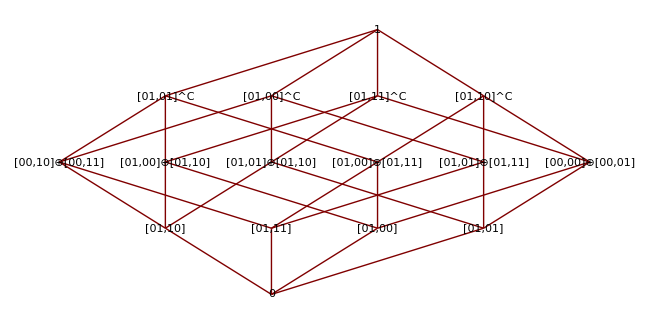

```mathematica
LayeredGraphPlot[subposet,Bottom, AspectRatio->.5, VertexLabeling->True, DirectedEdges->False]
```

Now we consider a subposet generated by q1,q2 thus two questions localized in the same subsystem.

```mathematica
subq2 = generateSubLattice@{q1,q2}
```

{question[{1,1},{1,1}]⊕question[{1,1},{1,2}],question[{1,1},{2,1}]⊕question[{1,1},{2,2}],question[{2,1},{1,1}]⊕question[{2,1},{1,2}],question[{2,1},{2,1}]⊕question[{2,1},{2,2}],question[0],question[1]}

```mathematica
printQ/@subq2
```

{[00,00]⊕[00,01],[00,10]⊕[00,11],[10,00]⊕[10,01],[10,10]⊕[10,11],0,1}

This look exactly like a part of qubit propositional system.

```mathematica
subq3 = generateSubLattice@{q1,q2,r1,r2};
```

We’ve got everything

```mathematica
Length[subq3]
```

82

Now we look for other possibly interesting localized observables

```mathematica
changeObs[q_question, 1]:=question[{Mod[q[[1,1]]-1+1,2]+1,q[[1,2]]},q[[2]]];
changeObs[q_question, 2]:=question[{q[[1,1]],Mod[q[[1,2]]-1+1,2]+1},q[[2]]];
changeObs[q_,s_]:=changeObs[#,s]&/@q
```

```mathematica
isLocalized[q_,s_]:=isQEqual[q,changeObs[q,Mod[s-1+1,2]+1]];
```

```mathematica
isLocalized[#,1]&/@{q1,q2,r1,r2}
```

{True,True,False,False}

```mathematica
local1 = Select[rank2questions, isLocalized[#,1]&];
local2 = Select[rank2questions, isLocalized[#,2]&];
```

```mathematica
local1nc=Select[Subsets[local1,{2}], Not[compatibilityTest[Sequence@@#]]&];
local2nc=Select[Subsets[local2,{2}], Not[compatibilityTest[Sequence@@#]]&];
```

```mathematica
isBoolAlgebra[p_]:=Select[Subsets[p,{3}], Not[distributivityTest[Sequence@@#]]&]=={}
```

```mathematica
ncsystems=Flatten[Outer[Join,local1nc,local2nc,1],1];
```

```mathematica
Length[generateSubLattice[#]]&/@ncsystems
```

{82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82}

```mathematica
nlsystems = Flatten[Outer[List, local1, local2],1];
```

```mathematica
compatibilityTest[Sequence@@#]&/@nlsystems
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
printQ/@local1
```

{[00,00]⊕[00,01],[00,10]⊕[00,11],[10,00]⊕[10,01],[10,10]⊕[10,11]}

```mathematica
nonlocal=Complement[rank2questions, local1, local2];
```

```mathematica
printQ/@nonlocal
```

{[00,00]⊕[00,11],[00,00]⊕[01,10],[00,00]⊕[01,11],[00,00]⊕[10,01],[00,00]⊕[10,11],[00,01]⊕[00,10],[00,01]⊕[01,10],[00,01]⊕[01,11],[00,01]⊕[10,00],[00,01]⊕[10,10],[00,10]⊕[01,00],[00,10]⊕[01,01],[00,10]⊕[10,01],[00,10]⊕[10,11],[00,11]⊕[01,00],[00,11]⊕[01,01],[00,11]⊕[10,00],[00,11]⊕[10,10],[01,00]⊕[01,11],[01,00]⊕[11,01],[01,00]⊕[11,11],[01,01]⊕[01,10],[01,01]⊕[11,00],[01,01]⊕[11,10],[01,10]⊕[11,01],[01,10]⊕[11,11],[01,11]⊕[11,00],[01,11]⊕[11,10],[10,00]⊕[10,11],[10,00]⊕[11,10],[10,00]⊕[11,11],[10,01]⊕[10,10],[10,01]⊕[11,10],[10,01]⊕[11,11],[10,10]⊕[11,00],[10,10]⊕[11,01],[10,11]⊕[11,00],[10,11]⊕[11,01],[11,00]⊕[11,11],[11,01]⊕[11,10]}

#### Non-UCP

In this section we check that Box World One is not a UCP space

```mathematica
q = question[{1,1},{1,1}]⊕question[{1,1},{1,2}];
```

```mathematica
printQ[q]
```

[00,00]⊕[00,01]

```mathematica
s1 = state[{
{1, 1, 1, 1},
{0, 0, 0, 0},
{0, 0, 0, 0},
{0, 0, 0, 0}}];
s2 = state[{
{1, 1, 0, 0},
{0, 0, 0, 0},
{0, 0, 1, 1},
{0, 0, 0, 0}}];
```

```mathematica
nsstate = state[{{1/2,1/2,1/2,0},{0,0,0,1/2},{0,0,0,1/2},{1/2,1/2,1/2,0}}];
```

```mathematica
pr[#,s1] pr[q,nsstate] == pr[#,nsstate]&/@lessThanList[q]
```

{True,True,True,True,True,True}

```mathematica
pr[#,s2] pr[q,nsstate] == pr[#,nsstate]&/@lessThanList[q]
```

{True,True,True,True,True,True}

```mathematica
pr[#,generalState[]] pr[q,nsstate] == pr[#,nsstate]&/@lessThanList[q]
```

{True,a11/2==1/2,a21/2==0,a12/2==1/2,a22/2==0,(a11+a21)/2==1/2}

```mathematica
FindInstance[And@@Join[And@@%,allowedStateRestr], Flatten[state2matrix[generalState[]]],2]
```

{{a11→1,a12→1,a13→0,a14→0,a21→0,a22→0,a23→0,a24→0,a31→0,a32→0,a33→1,a34→1,a41→0,a42→0,a43→0,a44→0},{a11→1,a12→1,a13→84/101,a14→84/101,a21→0,a22→0,a23→0,a24→0,a31→0,a32→0,a33→17/101,a34→17/101,a41→0,a42→0,a43→0,a44→0}}

```mathematica
MatrixForm[state2matrix[generalState[]/.#]]&/@%
```

{(1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0),(1 | 1 | 84/101 | 84/101
0 | 0 | 0 | 0
0 | 0 | 17/101 | 17/101
0 | 0 | 0 | 0)}

```mathematica
pr[#,generalCState[]] pr[q,nsstate] == pr[#,nsstate]&/@lessThanList[q]
```

{True,1/2 (c10+c11+c6+c7)==1/2,1/2 (c12+c5+c8+c9)==0,1/2 (c10+c12+c6+c8)==1/2,1/2 (c11+c5+c7+c9)==0,1/2 (c10+c11+c12+c5+c6+c7+c8+c9)==1/2}

```mathematica
FindInstance[And@@Join[And@@%,And@@convexCoeffRestr], convexCoeffs,2]
```

{{c1→0,c2→0,c3→0,c4→0,c5→0,c6→0,c7→0,c8→0,c9→0,c10→1,c11→0,c12→0,c13→0,c14→0,c15→0,c16→0},{c1→0,c2→0,c3→0,c4→0,c5→0,c6→84/101,c7→0,c8→0,c9→0,c10→17/101,c11→0,c12→0,c13→0,c14→0,c15→0,c16→0}}

```mathematica
MatrixForm[state2matrix[generalCState[]/.#]]&/@%
```

{(1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0),(1 | 1 | 84/101 | 84/101
0 | 0 | 0 | 0
0 | 0 | 17/101 | 17/101
0 | 0 | 0 | 0)}

#### Richness of states and concreteness

```mathematica
rho=generalState[]
```

state[{{a11,a12,a13,a14},{a21,a22,a23,a24},{a31,a32,a33,a34},{a41,a42,a43,a44}}]

```mathematica
vars =Flatten[state2matrix[rho]]
```

{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}

```mathematica
disjointQ[q_,p_]:=isLess[q,orthocmpl[p]]
```

```mathematica
notDisjointPairs=Select[Subsets[questions,{2}], Not[disjointQ[#[[1]],#[[2]]]]&];
```

```mathematica
Length[notDisjointPairs]
```

3032

```mathematica
FindInstance[allowedStateRestr&&pr[#[[1]],rho]==1&&pr[#[[2]],rho]>0,vars]≠{}&/@notDisjointPairs;
```

```mathematica
And@@%
```

True

```mathematica
twoValuedStates=Select[state[Partition[#,4]]&/@Tuples[{0,1},16], normalizationQ[#]&&nonsignalQ[#,1]&&nonsignalQ[#,2]&]
```

{state[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,1,1,1}}],state[{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,0,1,0}}],state[{{0,0,0,0},{0,0,0,0},{1,0,1,0},{0,1,0,1}}],state[{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,0,0,0}}],state[{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,0,0}}],state[{{0,0,0,0},{1,1,0,0},{0,0,0,0},{0,0,1,1}}],state[{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,0,0,0}}],state[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}],state[{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}],state[{{0,0,1,1},{0,0,0,0},{1,1,0,0},{0,0,0,0}}],state[{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}],state[{{0,1,0,1},{1,0,1,0},{0,0,0,0},{0,0,0,0}}],state[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}],state[{{1,0,1,0},{0,1,0,1},{0,0,0,0},{0,0,0,0}}],state[{{1,1,0,0},{0,0,0,0},{0,0,1,1},{0,0,0,0}}],state[{{1,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}

The same as classically correlated states

```mathematica
richTestForPair2[q1_,q2_]:=pr[q1,#]==1&&pr[q2,#]>0 &/@classicalStates
```

```mathematica
richTestForPair[q1_,q2_]:=Or@@(pr[q1,#]==1&&pr[q2,#]>0 &/@classicalStates)
```

```mathematica
richTestForPair[Sequence@@#]&/@notDisjointPairs;
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
And@@%
```

True

```mathematica
Length[classicalStates]
```

16

```mathematica
clStatesCertainForQuestion[q_]:=Select[classicalStates, pr[q,#]==1&]
delta = clStatesCertainForQuestion /@questions;
```

```mathematica
subsetQ[s_,r_]:=And@@(MemberQ[r,#,1]&/@s)
equalQ[s_,r_]:=And[subsetQ[s,r],subsetQ[r,s]]
isElement[e_,s_]:=Or@@(equalQ[e,#]&/@s)
```

```mathematica
subsetQ[s_,r_]:=If[Length[r]<Length[s],False,
Length[Intersection[s,r]]==Length[s]]
```

```mathematica
subsetQ[{a,b,c},{a,b,c,d,e}]
subsetQ[{a,b,c},{a,b,d,e}]
```

True

False

```mathematica
equalQ[{{b,c},a},{a,{b,c}}]
```

True

```mathematica
equalQ[{e},#]&/@{{a,b},{e},{e,d}}
```

{False,True,False}

```mathematica
isElement[a,{a,b,c,d}]
```

Intersection::normal: Nonatomic expression expected at position 1 in a ∩ a.

Intersection::normal: Nonatomic expression expected at position 1 in a ∩ b.

Intersection::normal: Nonatomic expression expected at position 1 in a ∩ c.

General::stop: Further output of Intersection :: normal will be suppressed during this calculation.

False

```mathematica
qIndex[q_]:=Position[questions,q,1][[1,1]]
testComplement[q_]:=equalQ[delta[[qIndex[orthocmpl[q]]]],Complement[classicalStates,delta[[qIndex[q]]]]]
testOrder[{p_,q_}/;isLess[p,q]]:=subsetQ[delta[[qIndex[p]]],delta[[qIndex[q]]]];
testOrder[{p_,q_}/;isLess[q,p]]:=testOrder[{q,p}];
testOrder[{p_,q_}]:=And[!subsetQ[delta[[qIndex[p]]],delta[[qIndex[q]]]],
!subsetQ[delta[[qIndex[q]]],delta[[qIndex[p]]]]]
```

```mathematica
And@@(testOrder/@Subsets[questions,{2}])
```

True

```mathematica
And@@(testComplement/@questions)
```

True

```mathematica
cpairs=Select[Subsets[delta,{2}], !subsetQ[#[[1]],#[[2]]]&&!subsetQ[#[[2]],#[[1]]]&];
```

```mathematica
ip=Intersection[Sequence@@#]&/@cpairs;
```

{{},{},«2821»,{state[{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,0,0}}],state[{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,0,0,0}}],state[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}],state[{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}}],state[{«1»}],state[{{0,1,0,1},{1,0,1,0},{0,0,0,0},{0,0,0,0}}],state[{{1,0,1,0},{0,1,0,1},{0,0,0,0},{0,0,0,0}}],state[{{1,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}}

```mathematica
isElement[#,delta]&/@delta
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Position[isElement[#,delta]&/@ip[[1;;10]],True]
```

{0.03541,{{1},{2},{3},{6},{7},{9}}}

```mathematica
Position[isElement[#,delta]&/@ip,True]
```

{{1},{2},{3},{6},{7},{9},{11},{16},{17},{18},{19},{22},{25},{26},{57},{66},{67},{70},{71},{72},{74},{80},{81},{82},{83},{86},{93},{94},{121},{130},{131},{132},{136},{138},{143},{144},{147},{148},{149},{154},{155},{184},{193},{194},{197},{199},{205},{206},{211},{214},{215},{216},{217},{246},{255},{256},{257},{263},{265},{278},{279},{282},{285},{286},{289},{290},{309},{316},{317},{322},{324},{338},{339},{342},{345},{346},{351},{352},{369},{376},{382},{384},{385},{388},{393},{404},{405},{406},{407},{428},{439},{441},{443},{446},{451},{462},{465},{466},{467},{486},{493},{494},{495},{498},{499},{507},{510},{518},{531},{532},{533},{534},{547},{550},{551},{554},{555},{557},{561},{570},{587},{588},{589},{590},{603},{606},{607},{608},{618},{621},{629},{642},{643},{648},{649},{658},{661},{662},{666},{670},{679},{696},{699},{702},{703},{712},{715},{716},{717},{744},{745},{748},{755},{756},{757},{758},{767},{768},{769},{792},{794},{798},{807},{808},{809},{810},{819},{820},{847},{848},{851},{852},{854},{856},{861},{870},{893},{895},{899},{902},{904},{906},{911},{920},{921},{922},{923},{924},{927},{928},{929},{930},{933},{934},{935},{938},{939},{942},{943},{946},{947},{968},{969},{970},{971},{980},{983},{984},{985},{986},{989},{990},{991},{994},{995},{998},{999},{1012},{1013},{1016},{1019},{1026},{1027},{1032},{1033},{1042},{1043},{1048},{1083},{1084},{1097},{1102},{1103},{1106},{1141},{1146},{1159},{1160},{1163},{1198},{1203},{1212},{1214},{1222},{1223},{1254},{1262},{1269},{1277},{1278},{1309},{1318},{1323},{1328},{1363},{1364},{1379},{1380},{1381},{1384},{1385},{1388},{1389},{1402},{1403},{1406},{1409},{1416},{1417},{1422},{1423},{1428},{1431},{1466},{1471},{1482},{1517},{1522},{1531},{1539},{1540},{1568},{1574},{1588},{1589},{1617},{1624},{1630},{1631},{1634},{1635},{1638},{1639},{1642},{1643},{1664},{1665},{1666},{1667},{1676},{1679},{1680},{1711},{1712},{1725},{1726},{1757},{1758},{1769},{1801},{1808},{1845},{1853},{1858},{1889},{1890},{1931},{1932},{1943},{1972},{1977},{2012},{2018},{2024},{2025},{2026},{2027},{2028},{2029},{2030},{2031},{2032},{2033},{2034},{2035},{2042},{2047},{2048},{2053},{2054},{2059},{2060},{2063},{2064},{2089},{2090},{2099},{2101},{2104},{2105},{2126},{2134},{2137},{2140},{2141},{2162},{2171},{2172},{2197},{2198},{2207},{2208},{2209},{2210},{2211},{2212},{2213},{2220},{2225},{2226},{2231},{2232},{2237},{2238},{2239},{2242},{2243},{2263},{2269},{2274},{2275},{2295},{2302},{2304},{2326},{2333},{2356},{2364},{2365},{2386},{2391},{2414},{2420},{2422},{2423},{2424},{2425},{2426},{2427},{2428},{2429},{2430},{2431},{2432},{2433},{2434},{2443},{2444},{2445},{2446},{2449},{2452},{2467},{2468},{2473},{2475},{2476},{2477},{2492},{2497},{2499},{2500},{2501},{2516},{2521},{2524},{2539},{2540},{2545},{2546},{2561},{2566},{2567},{2582},{2587},{2588},{2589},{2590},{2591},{2592},{2593},{2602},{2603},{2604},{2605},{2606},{2607},{2608},{2621},{2622},{2625},{2626},{2639},{2640},{2643},{2656},{2657},{2672},{2673},{2676},{2689},{2690},{2703},{2704},{2705},{2706},{2707},{2710},{2711},{2713},{2715},{2720},{2721},{2724},{2725},{2726},{2728},{2734},{2735},{2736},{2740},{2742},{2747},{2748},{2751},{2753},{2759},{2760},{2761},{2767},{2769},{2770},{2771},{2776},{2778},{2780},{2786},{2788},{2793},{2795},{2797},{2798},{2799},{2802},{2803},{2804},{2805},{2808},{2809},{2810},{2811},{2812},{2815},{2816},{2819},{2820},{2821},{2822},{2823},{2824}}

```mathematica
qIndex[q_]:=Position[questions,q,1][[1,1]]
testComplement[q_]:=equalQ[phaseSpaceSet[orthocmpl[q]],Complement[Range[16],phaseSpaceSet[q]]]
testOrder[{p_,q_}/;isLess[p,q]]:=subsetQ[phaseSpaceSet[p],phaseSpaceSet[q]];
testOrder[{p_,q_}/;isLess[q,p]]:=testOrder[{q,p}];
testOrder[{p_,q_}]:=And[!subsetQ[phaseSpaceSet[p],phaseSpaceSet[q]],
!subsetQ[phaseSpaceSet[q],phaseSpaceSet[p]]]
```

```mathematica
And@@(testComplement/@questions)
```

True

```mathematica
And@@(testOrder/@Subsets[questions,{2}])
```

True

#### Completness of states

```mathematica
disjointQ[q_,p_]:=isLess[q,orthocmpl[p]];
pairWiseDisjoint[l_]:=And@@(disjointQ[#[[1]],#[[2]]]&/@Subsets[l,{2}])
disjointPairs=Select[Subsets[questions,{2}],disjointQ[#[[1]],#[[2]]]&];
```

```mathematica
restr =Join[normalizationQ[generalState[]],positivityQ[generalState[]]]
```

a11+a21+a31+a41==1&&a12+a22+a32+a42==1&&a13+a23+a33+a43==1&&a14+a24+a34+a44==1&&a11≥0&&a12≥0&&a13≥0&&a14≥0&&a21≥0&&a22≥0&&a23≥0&&a24≥0&&a31≥0&&a32≥0&&a33≥0&&a34≥0&&a41≥0&&a42≥0&&a43≥0&&a44≥0

```mathematica
rho=generalState[]
```

state[{{a11,a12,a13,a14},{a21,a22,a23,a24},{a31,a32,a33,a34},{a41,a42,a43,a44}}]

```mathematica
vars =Flatten[state2matrix[rho]]
```

{a11,a12,a13,a14,a21,a22,a23,a24,a31,a32,a33,a34,a41,a42,a43,a44}

```mathematica
orderConditionForQ[q_]:=FullSimplify[And@@(Reduce[ForAll[vars, pr[q,rho]≤pr[#,rho]],vars]&/@greaterThanList[q]), Assumptions:>restr]
```

```mathematica
orderConditionForQ[questions[[3]]]
```

a32≤a21+a31+a41&&a42≤a21+a31+a41&&a23≤a21+a31+a41&&a43≤a21+a31+a41

```mathematica
oc=Flatten[orderConditionForQ[#]&/@questions];
```

```mathematica
oc
```

{True,True,a32≤a21+a31+a41&&a42≤a21+a31+a41&&a23≤a21+a31+a41&&a43≤a21+a31+a41,a21+a32≤1&&a21+a42≤1&&a21≤a23+a33+a43&&a21+a33≤1,a31≤a22+a32+a42&&a22+a31≤1&&a23+a31≤1&&a31+a43≤1,a41≤a22+a32+a42&&a22+a41≤1&&a41≤a23+a33+a43&&a33+a41≤1,a11+a21≥a12&&a24≤a22+a32+a42&&a44≤a22+a32+a42,a22≤a11+a21&&a22≤a24+a34+a44&&a22+a34≤1,a31+a41≥a32&&a24+a32≤1&&a32+a44≤1,a42≤a31+a41&&a42≤a24+a34+a44&&a34+a42≤1,a11+a31≥a13&&a34≤a23+a33+a43&&a44≤a23+a33+a43,a21+a41≥a23&&a23+a34≤1&&a23+a44≤1,a33≤a11+a31&&a33≤a24+a34+a44&&a24+a33≤1,a43≤a21+a41&&a43≤a24+a34+a44&&a24+a43≤1,a12+a32≥a14&&a13+a23≥a14,a22+a42≥a24&&a24≤a13+a23,a33+a43≥a34&&a34≤a12+a32,a44≤a22+a42&&a44≤a33+a43,a32≤a31+a41&&a42≤a31+a41,a23≤a21+a41&&a43≤a21+a41,True,a32≤a31+a41&&a32+a42≤a21+a31+a41,a42≤a31+a41&&a32+a42≤a21+a31+a41,a23≤a21+a41&&a23+a43≤a21+a31+a41,a23+a43≤a21+a31+a41&&a43≤a21+a41,True,a21+a41≤a23+a33+a43&&a21+a33+a41≤1,a32≤a31+a41&&a21+a32+a42≤1,a42≤a31+a41&&a21+a32+a42≤1,a21≤a23+a43&&a21+a41≤a23+a33+a43,a21≤a23+a43&&a21+a33+a41≤1,a31+a41≤a22+a32+a42&&a22+a31+a41≤1,a31≤a32+a42&&a31+a41≤a22+a32+a42,a31≤a32+a42&&a22+a31+a41≤1,a23≤a21+a41&&a23+a31+a43≤1,a43≤a21+a41&&a23+a31+a43≤1,a41≤a32+a42&&a31+a41≤a22+a32+a42,a41≤a32+a42&&a22+a31+a41≤1,a21+a41≤a23+a33+a43&&a41≤a23+a43,a41≤a23+a43&&a21+a33+a41≤1,a24≤a22+a42&&a44≤a22+a42,True,a24≤a22+a42&&a24+a44≤a22+a32+a42,a24+a44≤a22+a32+a42&&a44≤a22+a42,True,a22+a42≤a24+a34+a44&&a22+a34+a42≤1,a22≤a24+a44&&a22+a42≤a24+a34+a44,a22≤a24+a44&&a22+a34+a42≤1,a24≤a22+a42&&a24+a32+a44≤1,a44≤a22+a42&&a24+a32+a44≤1,a22+a42≤a24+a34+a44&&a42≤a24+a44,a42≤a24+a44&&a22+a34+a42≤1,a34≤a33+a43&&a44≤a33+a43,True,a34≤a33+a43&&a34+a44≤a23+a33+a43,a44≤a33+a43&&a34+a44≤a23+a33+a43,True,a34≤a33+a43&&a23+a34+a44≤1,a44≤a33+a43&&a23+a34+a44≤1,a33+a43≤a24+a34+a44&&a24+a33+a43≤1,a33≤a34+a44&&a33+a43≤a24+a34+a44,a33≤a34+a44&&a24+a33+a43≤1,a43≤a34+a44&&a33+a43≤a24+a34+a44,a43≤a34+a44&&a24+a33+a43≤1,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
redoc=Simplify[And@@oc, Assumptions:>restr]
```

a11+a21≥a12&&a31+a41≥a32&&a11+a31≥a13&&a21+a41≥a23&&a12+a32≥a14&&a13+a23≥a14&&a22+a42≥a24&&a33+a43≥a34&&a21+a31+a41≥a32&&a21+a31+a41≥a42&&a21+a31+a41≥a23&&a21+a31+a41≥a43&&a21+a32≤1&&a21+a42≤1&&a21≤a23+a33+a43&&a21+a33≤1&&a22+a32+a42≥a31&&a22+a31≤1&&a23+a31≤1&&a31+a43≤1&&a22+a32+a42≥a41&&a22+a41≤1&&a23+a33+a43≥a41&&a33+a41≤1&&a22+a32+a42≥a24&&a22+a32+a42≥a44&&a11+a21≥a22&&a22≤a24+a34+a44&&a22+a34≤1&&a24+a32≤1&&a32+a44≤1&&a31+a41≥a42&&a24+a34+a44≥a42&&a34+a42≤1&&a23+a33+a43≥a34&&a23+a33+a43≥a44&&a23+a34≤1&&a23+a44≤1&&a11+a31≥a33&&a24+a34+a44≥a33&&a24+a33≤1&&a21+a41≥a43&&a24+a34+a44≥a43&&a24+a43≤1&&a13+a23≥a24&&a12+a32≥a34&&a22+a42≥a44&&a33+a43≥a44&&a21+a31+a41≥a32+a42&&a21+a31+a41≥a23+a43&&a21+a41≤a23+a33+a43&&a21+a33+a41≤1&&a21+a32+a42≤1&&a21≤a23+a43&&a22+a32+a42≥a31+a41&&a22+a31+a41≤1&&a31≤a32+a42&&a23+a31+a43≤1&&a32+a42≥a41&&a23+a43≥a41&&a22+a32+a42≥a24+a44&&a22+a42≤a24+a34+a44&&a22+a34+a42≤1&&a22≤a24+a44&&a24+a32+a44≤1&&a24+a44≥a42&&a23+a33+a43≥a34+a44&&a23+a34+a44≤1&&a24+a34+a44≥a33+a43&&a24+a33+a43≤1&&a33≤a34+a44&&a34+a44≥a43

```mathematica
rr = rho/.FindInstance[redoc&&restr&&(Not[nonsignalQ[rho,1]&&nonsignalQ[rho,2]]),vars][[1]]
```

state[{{1/3,1/3,0,0},{0,1/3,1/3,1/3},{1/3,1/3,1/3,1/3},{1/3,0,1/3,1/3}}]

```mathematica
Function[q,pr[q,rr]≤pr[#,rr]&/@greaterThanList[q]]/@questions
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True}}

```mathematica
redoc=Select[oc,FindInstance[restr&&Not[#],vars]≠{}&]
```

{a11≤1-a32,a11≤1-a42,a11≤1-a23,a11≤1-a43,a21≤1-a32,a21≤1-a42,a21≤1-a13,a21≤1-a33,a31≤1-a12,a31≤1-a22,a31≤1-a23,a31≤1-a43,a41≤1-a12,a41≤1-a22,a41≤1-a13,a41≤1-a33,a12≤a11+a21,a12≤1-a31,a12≤1-a41,a12≤1-a24,a12≤1-a44,a22≤a11+a21,a22≤1-a31,a22≤1-a41,a22≤1-a14,a22≤1-a34,a32≤a31+a41,a32≤1-a11,a32≤1-a21,a32≤1-a24,a32≤1-a44,a42≤a31+a41,a42≤1-a11,a42≤1-a21,a42≤1-a14,a42≤1-a34,a13≤a11+a31,a13≤1-a21,a13≤1-a41,a13≤1-a34,a13≤1-a44,a23≤a21+a41,a23≤1-a11,a23≤1-a31,a23≤1-a34,a23≤1-a44,a33≤a11+a31,a33≤1-a21,a33≤1-a41,a33≤1-a14,a33≤1-a24,a43≤a21+a41,a43≤1-a11,a43≤1-a31,a43≤1-a14,a43≤1-a24,a14≤a12+a32,a14≤a13+a23,a14≤1-a22,a14≤1-a42,a14≤1-a33,a14≤1-a43,a24≤a22+a42,a24≤a13+a23,a24≤1-a12,a24≤1-a32,a24≤1-a33,a24≤1-a43,a34≤a12+a32,a34≤a33+a43,a34≤1-a22,a34≤1-a42,a34≤1-a13,a34≤1-a23,a44≤a22+a42,a44≤a33+a43,a44≤1-a12,a44≤1-a32,a44≤1-a13,a44≤1-a23,a11+a21≤1-a32,a11+a21≤1-a42,a11+a31≤1-a23,a11+a31≤1-a43,a11+a32≤1,a11+a32≤1-a21,a11+a32≤1-a42,a11+a42≤1,a11+a42≤1-a21,a11+a42≤1-a32,a11+a23≤1,a11+a23≤1-a31,a11+a23≤1-a43,a11+a43≤1,a11+a43≤1-a31,a11+a43≤1-a23,a21+a41≤1-a13,a21+a41≤1-a33,a21+a32≤1,a21+a32≤1-a11,a21+a32≤1-a42,a21+a42≤1,a21+a42≤1-a11,a21+a42≤1-a32,a13+a21≤1,a13+a21≤1-a41,a13+a21≤1-a33,a21+a33≤1,a21+a33≤1-a41,a21+a33≤1-a13,a31+a41≤1-a12,a31+a41≤1-a22,a12+a31≤1,a12+a31≤1-a41,a12+a31≤1-a22,a22+a31≤1,a22+a31≤1-a41,a22+a31≤1-a12,a23+a31≤1,a23+a31≤1-a11,a23+a31≤1-a43,a31+a43≤1,a31+a43≤1-a11,a31+a43≤1-a23,a12+a41≤1,a12+a41≤1-a31,a12+a41≤1-a22,a22+a41≤1,a22+a41≤1-a31,a22+a41≤1-a12,a13+a41≤1,a13+a41≤1-a21,a13+a41≤1-a33,a33+a41≤1,a33+a41≤1-a21,a33+a41≤1-a13,a12+a32≤1-a24,a12+a32≤1-a44,a12+a24≤1,a12+a24≤1-a32,a12+a24≤1-a44,a12+a44≤1,a12+a44≤1-a32,a12+a44≤1-a24,a22+a42≤1-a14,a22+a42≤1-a34,a14+a22≤1,a14+a22≤1-a42,a14+a22≤1-a34,a22+a34≤1,a22+a34≤1-a42,a22+a34≤1-a14,a24+a32≤1,a24+a32≤1-a12,a24+a32≤1-a44,a32+a44≤1,a32+a44≤1-a12,a32+a44≤1-a24,a14+a42≤1,a14+a42≤1-a22,a14+a42≤1-a34,a34+a42≤1,a34+a42≤1-a22,a34+a42≤1-a14,a13+a23≤1-a34,a13+a23≤1-a44,a13+a34≤1,a13+a34≤1-a23,a13+a34≤1-a44,a13+a44≤1,a13+a44≤1-a23,a13+a44≤1-a34,a23+a34≤1,a23+a34≤1-a13,a23+a34≤1-a44,a23+a44≤1,a23+a44≤1-a13,a23+a44≤1-a34,a33+a43≤1-a14,a33+a43≤1-a24,a14+a33≤1,a14+a33≤1-a43,a14+a33≤1-a24,a24+a33≤1,a24+a33≤1-a43,a24+a33≤1-a14,a14+a43≤1,a14+a43≤1-a33,a14+a43≤1-a24,a24+a43≤1,a24+a43≤1-a33,a24+a43≤1-a14}

```mathematica
Join[And@@oc, allowedStateRestr]//Simplify
```

a11≥0&&a21≥0&&a31≥0&&a41≥0&&a32≥0&&a42≥0&&a23≥0&&a43≥0&&a13≥0&&a33≥0&&a12≥0&&a22≥0&&a24≥0&&a44≥0&&a14≥0&&a34≥0&&a21≤1&&a31≤1&&a41≤1&&a32≤1&&a42≤1&&a23≤1&&a43≤1&&a11≤1&&a13≤1&&a33≤1&&a12≤1&&a22≤1&&a24≤1&&a44≤1&&a14≤1&&a34≤1&&a11+a21+a32≤1&&a11+a21+a42≤1&&a11+a23+a31≤1&&a11+a31+a43≤1&&a11+a32+a42≤1&&a11+a23+a43≤1&&a13+a21+a41≤1&&a21+a33+a41≤1&&a21+a32+a42≤1&&a13+a21+a33≤1&&a12+a31+a41≤1&&a22+a31+a41≤1&&a12+a22+a31≤1&&a23+a31+a43≤1&&a12+a22+a41≤1&&a13+a33+a41≤1&&a12+a24+a32≤1&&a12+a32+a44≤1&&a12+a24+a44≤1&&a14+a22+a42≤1&&a22+a34+a42≤1&&a14+a22+a34≤1&&a24+a32+a44≤1&&a14+a34+a42≤1&&a13+a23+a34≤1&&a13+a23+a44≤1&&a13+a34+a44≤1&&a23+a34+a44≤1&&a14+a33+a43≤1&&a24+a33+a43≤1&&a14+a24+a33≤1&&a14+a24+a43≤1&&a11+a21==a12+a22&&a13+a23==a14+a24&&a31+a41==a32+a42&&a33+a43==a34+a44&&a11+a31==a13+a33&&a12+a32==a14+a34&&a21+a41==a23+a43&&a22+a42==a24+a44&&a11+a21+a31+a41==1&&a12+a22+a32+a42==1&&a13+a23+a33+a43==1&&a14+a24+a34+a44==1

```mathematica
a+b≤1&& 1≤a+b//FullSimplify
```

a+b==1

```mathematica
oc//TableForm
```

True
True
0≤a11
0≤a21
0≤a31
0≤a41
0≤a12
0≤a22
0≤a32
0≤a42
0≤a13
0≤a23
0≤a33
0≤a43
0≤a14
0≤a24
0≤a34
0≤a44
0≤a11+a21
0≤a11+a31
0≤a11+a41
0≤a11+a32
0≤a11+a42
0≤a11+a23
0≤a11+a43
0≤a21+a31
0≤a21+a41
0≤a21+a32
0≤a21+a42
0≤a13+a21
0≤a21+a33
0≤a31+a41
0≤a12+a31
0≤a22+a31
0≤a23+a31
0≤a31+a43
0≤a12+a41
0≤a22+a41
0≤a13+a41
0≤a33+a41
0≤a12+a32
0≤a12+a42
0≤a12+a24
0≤a12+a44
0≤a22+a32
0≤a22+a42
0≤a14+a22
0≤a22+a34
0≤a24+a32
0≤a32+a44
0≤a14+a42
0≤a34+a42
0≤a13+a23
0≤a13+a43
0≤a13+a34
0≤a13+a44
0≤a23+a33
0≤a23+a34
0≤a23+a44
0≤a33+a43
0≤a14+a33
0≤a24+a33
0≤a14+a43
0≤a24+a43
0≤a14+a44
0≤a24+a34
0≤1-a11
0≤1-a21
0≤1-a31
0≤1-a41
0≤1-a12
0≤1-a22
0≤1-a32
0≤1-a42
0≤1-a13
0≤1-a23
0≤1-a33
0≤1-a43
0≤1-a14
0≤1-a24
0≤1-a34
0≤1-a44
True
a11≤1
a11≤a11
a11≤a11+a21
a11≤a11+a31
a11≤a11+a41
a11≤a11+a32
a11≤a11+a42
a11≤a11+a23
a11≤a11+a43
a11≤1-a21
a11≤1-a31
a11≤1-a41
a11≤1-a32
a11≤1-a42
a11≤1-a23
a11≤1-a43
a21≤1
a21≤a21
a21≤a11+a21
a21≤a21+a31
a21≤a21+a41
a21≤a21+a32
a21≤a21+a42
a21≤a13+a21
a21≤a21+a33
a21≤1-a11
a21≤1-a31
a21≤1-a41
a21≤1-a32
a21≤1-a42
a21≤1-a13
a21≤1-a33
a31≤1
a31≤a31
a31≤a11+a31
a31≤a21+a31
a31≤a31+a41
a31≤a12+a31
a31≤a22+a31
a31≤a23+a31
a31≤a31+a43
a31≤1-a11
a31≤1-a21
a31≤1-a41
a31≤1-a12
a31≤1-a22
a31≤1-a23
a31≤1-a43
a41≤1
a41≤a41
a41≤a11+a41
a41≤a21+a41
a41≤a31+a41
a41≤a12+a41
a41≤a22+a41
a41≤a13+a41
a41≤a33+a41
a41≤1-a11
a41≤1-a21
a41≤1-a31
a41≤1-a12
a41≤1-a22
a41≤1-a13
a41≤1-a33
a12≤1
a12≤a12
a12≤a11+a21
a12≤a12+a31
a12≤a12+a41
a12≤a12+a32
a12≤a12+a42
a12≤a12+a24
a12≤a12+a44
a12≤1-a31
a12≤1-a41
a12≤1-a22
a12≤1-a32
a12≤1-a42
a12≤1-a24
a12≤1-a44
a22≤1
a22≤a22
a22≤a11+a21
a22≤a22+a31
a22≤a22+a41
a22≤a22+a32
a22≤a22+a42
a22≤a14+a22
a22≤a22+a34
a22≤1-a31
a22≤1-a41
a22≤1-a12
a22≤1-a32
a22≤1-a42
a22≤1-a14
a22≤1-a34
a32≤1
a32≤a32
a32≤a11+a32
a32≤a21+a32
a32≤a31+a41
a32≤a12+a32
a32≤a22+a32
a32≤a24+a32
a32≤a32+a44
a32≤1-a11
a32≤1-a21
a32≤1-a12
a32≤1-a22
a32≤1-a42
a32≤1-a24
a32≤1-a44
a42≤1
a42≤a42
a42≤a11+a42
a42≤a21+a42
a42≤a31+a41
a42≤a12+a42
a42≤a22+a42
a42≤a14+a42
a42≤a34+a42
a42≤1-a11
a42≤1-a21
a42≤1-a12
a42≤1-a22
a42≤1-a32
a42≤1-a14
a42≤1-a34
a13≤1
a13≤a13
a13≤a11+a31
a13≤a13+a21
a13≤a13+a41
a13≤a13+a23
a13≤a13+a43
a13≤a13+a34
a13≤a13+a44
a13≤1-a21
a13≤1-a41
a13≤1-a23
a13≤1-a33
a13≤1-a43
a13≤1-a34
a13≤1-a44
a23≤1
a23≤a23
a23≤a11+a23
a23≤a21+a41
a23≤a23+a31
a23≤a13+a23
a23≤a23+a33
a23≤a23+a34
a23≤a23+a44
a23≤1-a11
a23≤1-a31
a23≤1-a13
a23≤1-a33
a23≤1-a43
a23≤1-a34
a23≤1-a44
a33≤1
a33≤a33
a33≤a11+a31
a33≤a21+a33
a33≤a33+a41
a33≤a23+a33
a33≤a33+a43
a33≤a14+a33
a33≤a24+a33
a33≤1-a21
a33≤1-a41
a33≤1-a13
a33≤1-a23
a33≤1-a43
a33≤1-a14
a33≤1-a24
a43≤1
a43≤a43
a43≤a11+a43
a43≤a21+a41
a43≤a31+a43
a43≤a13+a43
a43≤a33+a43
a43≤a14+a43
a43≤a24+a43
a43≤1-a11
a43≤1-a31
a43≤1-a13
a43≤1-a23
a43≤1-a33
a43≤1-a14
a43≤1-a24
a14≤1
a14≤a14
a14≤a12+a32
a14≤a14+a22
a14≤a14+a42
a14≤a13+a23
a14≤a14+a33
a14≤a14+a43
a14≤a14+a44
a14≤1-a22
a14≤1-a42
a14≤1-a33
a14≤1-a43
a14≤1-a24
a14≤1-a34
a14≤1-a44
a24≤1
a24≤a24
a24≤a12+a24
a24≤a22+a42
a24≤a24+a32
a24≤a13+a23
a24≤a24+a33
a24≤a24+a43
a24≤a24+a34
a24≤1-a12
a24≤1-a32
a24≤1-a33
a24≤1-a43
a24≤1-a14
a24≤1-a34
a24≤1-a44
a34≤1
a34≤a34
a34≤a12+a32
a34≤a22+a34
a34≤a34+a42
a34≤a13+a34
a34≤a23+a34
a34≤a33+a43
a34≤a24+a34
a34≤1-a22
a34≤1-a42
a34≤1-a13
a34≤1-a23
a34≤1-a14
a34≤1-a24
a34≤1-a44
a44≤1
a44≤a44
a44≤a12+a44
a44≤a22+a42
a44≤a32+a44
a44≤a13+a44
a44≤a23+a44
a44≤a33+a43
a44≤a14+a44
a44≤1-a12
a44≤1-a32
a44≤1-a13
a44≤1-a23
a44≤1-a14
a44≤1-a24
a44≤1-a34
a11+a21≤1
a11+a21≤a11+a21
a11+a21≤1-a31
a11+a21≤1-a41
a11+a21≤1-a32
a11+a21≤1-a42
a11+a31≤1
a11+a31≤a11+a31
a11+a31≤1-a21
a11+a31≤1-a41
a11+a31≤1-a23
a11+a31≤1-a43
a11+a41≤1
a11+a41≤a11+a41
a11+a41≤1-a21
a11+a41≤1-a31
a11+a32≤1
a11+a32≤a11+a32
a11+a32≤1-a21
a11+a32≤1-a42
a11+a42≤1
a11+a42≤a11+a42
a11+a42≤1-a21
a11+a42≤1-a32
a11+a23≤1
a11+a23≤a11+a23
a11+a23≤1-a31
a11+a23≤1-a43
a11+a43≤1
a11+a43≤a11+a43
a11+a43≤1-a31
a11+a43≤1-a23
a21+a31≤1
a21+a31≤a21+a31
a21+a31≤1-a11
a21+a31≤1-a41
a21+a41≤1
a21+a41≤a21+a41
a21+a41≤1-a11
a21+a41≤1-a31
a21+a41≤1-a13
a21+a41≤1-a33
a21+a32≤1
a21+a32≤a21+a32
a21+a32≤1-a11
a21+a32≤1-a42
a21+a42≤1
a21+a42≤a21+a42
a21+a42≤1-a11
a21+a42≤1-a32
a13+a21≤1
a13+a21≤a13+a21
a13+a21≤1-a41
a13+a21≤1-a33
a21+a33≤1
a21+a33≤a21+a33
a21+a33≤1-a41
a21+a33≤1-a13
a31+a41≤1
a31+a41≤a31+a41
a31+a41≤1-a11
a31+a41≤1-a21
a31+a41≤1-a12
a31+a41≤1-a22
a12+a31≤1
a12+a31≤a12+a31
a12+a31≤1-a41
a12+a31≤1-a22
a22+a31≤1
a22+a31≤a22+a31
a22+a31≤1-a41
a22+a31≤1-a12
a23+a31≤1
a23+a31≤a23+a31
a23+a31≤1-a11
a23+a31≤1-a43
a31+a43≤1
a31+a43≤a31+a43
a31+a43≤1-a11
a31+a43≤1-a23
a12+a41≤1
a12+a41≤a12+a41
a12+a41≤1-a31
a12+a41≤1-a22
a22+a41≤1
a22+a41≤a22+a41
a22+a41≤1-a31
a22+a41≤1-a12
a13+a41≤1
a13+a41≤a13+a41
a13+a41≤1-a21
a13+a41≤1-a33
a33+a41≤1
a33+a41≤a33+a41
a33+a41≤1-a21
a33+a41≤1-a13
a12+a32≤1
a12+a32≤a12+a32
a12+a32≤1-a22
a12+a32≤1-a42
a12+a32≤1-a24
a12+a32≤1-a44
a12+a42≤1
a12+a42≤a12+a42
a12+a42≤1-a22
a12+a42≤1-a32
a12+a24≤1
a12+a24≤a12+a24
a12+a24≤1-a32
a12+a24≤1-a44
a12+a44≤1
a12+a44≤a12+a44
a12+a44≤1-a32
a12+a44≤1-a24
a22+a32≤1
a22+a32≤a22+a32
a22+a32≤1-a12
a22+a32≤1-a42
a22+a42≤1
a22+a42≤a22+a42
a22+a42≤1-a12
a22+a42≤1-a32
a22+a42≤1-a14
a22+a42≤1-a34
a14+a22≤1
a14+a22≤a14+a22
a14+a22≤1-a42
a14+a22≤1-a34
a22+a34≤1
a22+a34≤a22+a34
a22+a34≤1-a42
a22+a34≤1-a14
a24+a32≤1
a24+a32≤a24+a32
a24+a32≤1-a12
a24+a32≤1-a44
a32+a44≤1
a32+a44≤a32+a44
a32+a44≤1-a12
a32+a44≤1-a24
a14+a42≤1
a14+a42≤a14+a42
a14+a42≤1-a22
a14+a42≤1-a34
a34+a42≤1
a34+a42≤a34+a42
a34+a42≤1-a22
a34+a42≤1-a14
a13+a23≤1
a13+a23≤a13+a23
a13+a23≤1-a33
a13+a23≤1-a43
a13+a23≤1-a34
a13+a23≤1-a44
a13+a43≤1
a13+a43≤a13+a43
a13+a43≤1-a23
a13+a43≤1-a33
a13+a34≤1
a13+a34≤a13+a34
a13+a34≤1-a23
a13+a34≤1-a44
a13+a44≤1
a13+a44≤a13+a44
a13+a44≤1-a23
a13+a44≤1-a34
a23+a33≤1
a23+a33≤a23+a33
a23+a33≤1-a13
a23+a33≤1-a43
a23+a34≤1
a23+a34≤a23+a34
a23+a34≤1-a13
a23+a34≤1-a44
a23+a44≤1
a23+a44≤a23+a44
a23+a44≤1-a13
a23+a44≤1-a34
a33+a43≤1
a33+a43≤a33+a43
a33+a43≤1-a13
a33+a43≤1-a23
a33+a43≤1-a14
a33+a43≤1-a24
a14+a33≤1
a14+a33≤a14+a33
a14+a33≤1-a43
a14+a33≤1-a24
a24+a33≤1
a24+a33≤a24+a33
a24+a33≤1-a43
a24+a33≤1-a14
a14+a43≤1
a14+a43≤a14+a43
a14+a43≤1-a33
a14+a43≤1-a24
a24+a43≤1
a24+a43≤a24+a43
a24+a43≤1-a33
a24+a43≤1-a14
a14+a44≤1
a14+a44≤a14+a44
a14+a44≤1-a24
a14+a44≤1-a34
a24+a34≤1
a24+a34≤a24+a34
a24+a34≤1-a14
a24+a34≤1-a44
1-a11≤1
1-a11≤1-a11
1-a21≤1
1-a21≤1-a21
1-a31≤1
1-a31≤1-a31
1-a41≤1
1-a41≤1-a41
1-a12≤1
1-a12≤1-a12
1-a22≤1
1-a22≤1-a22
1-a32≤1
1-a32≤1-a32
1-a42≤1
1-a42≤1-a42
1-a13≤1
1-a13≤1-a13
1-a23≤1
1-a23≤1-a23
1-a33≤1
1-a33≤1-a33
1-a43≤1
1-a43≤1-a43
1-a14≤1
1-a14≤1-a14
1-a24≤1
1-a24≤1-a24
1-a34≤1
1-a34≤1-a34
1-a44≤1
1-a44≤1-a44

```mathematica
Not[allowedStateRestr]
```

!(a11+a21==a12+a22&&a13+a23==a14+a24&&a31+a41==a32+a42&&a33+a43==a34+a44&&a11+a31==a13+a33&&a12+a32==a14+a34&&a21+a41==a23+a43&&a22+a42==a24+a44&&a11+a21+a31+a41==1&&a12+a22+a32+a42==1&&a13+a23+a33+a43==1&&a14+a24+a34+a44==1&&a11≥0&&a12≥0&&a13≥0&&a14≥0&&a21≥0&&a22≥0&&a23≥0&&a24≥0&&a31≥0&&a32≥0&&a33≥0&&a34≥0&&a41≥0&&a42≥0&&a43≥0&&a44≥0)

```mathematica
rr =state[{{1/3,1/3,0,0},{0,1/3,1/3,1/3},{1/3,1/3,1/3,1/3},{1/3,0,1/3,1/3}}]
```

state[{{1/3,1/3,0,0},{0,1/3,1/3,1/3},{1/3,1/3,1/3,1/3},{1/3,0,1/3,1/3}}]

```mathematica
pairrestr=And@@(pr[join[#[[1]],#[[2]]][[1]],rho]==(pr[#[[1]],rho]+pr[#[[2]],rho])&/@disjointPairs)//Simplify
```

a11+a21+a31+a41==1&&a11+a21+a32+a42==1&&a11+a23+a31+a43==1&&a13+a21+a33+a41==1&&a12+a22+a31+a41==1&&a11+a21==a12+a22&&a12+a22+a32+a42==1&&a12+a24+a32+a44==1&&a14+a22+a34+a42==1&&a31+a41==a32+a42&&a11+a31==a13+a33&&a13+a23+a33+a43==1&&a13+a23+a34+a44==1&&a21+a41==a23+a43&&a14+a24+a33+a43==1&&a13+a23==a14+a24&&a12+a32==a14+a34&&a14+a24+a34+a44==1&&a22+a42==a24+a44&&a33+a43==a34+a44

```mathematica
printQ /@#&/@Take[disjointPairs,-8]
```

{{[01,01]⊕[11,10],[01,11]⊕[11,00]},{[10,00]⊕[10,01],[10,10]⊕[10,11]},{[10,00]⊕[10,11],[10,01]⊕[10,10]},{[10,00]⊕[11,10],[10,01]⊕[11,11]},{[10,00]⊕[11,11],[10,01]⊕[11,10]},{[10,10]⊕[11,00],[10,11]⊕[11,01]},{[10,10]⊕[11,01],[10,11]⊕[11,00]},{[11,00]⊕[11,11],[11,01]⊕[11,10]}}

```mathematica
Map[isLocalized[#,1]&, Take[disjointPairs,-8], {2}]
```

{{False,False},{True,True},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}}

```mathematica
Map[isLocalized[#,2]&, Take[disjointPairs,-8], {2}]
```

{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False}}

```mathematica
restr
```

a11+a21+a31+a41==1&&a12+a22+a32+a42==1&&a13+a23+a33+a43==1&&a14+a24+a34+a44==1&&a11≥0&&a12≥0&&a13≥0&&a14≥0&&a21≥0&&a22≥0&&a23≥0&&a24≥0&&a31≥0&&a32≥0&&a33≥0&&a34≥0&&a41≥0&&a42≥0&&a43≥0&&a44≥0

```mathematica
TableForm[List@@(pairrestr&&restr//FullSimplify)]
```

a11≥0
a12≥0
a13≥0
a14≥0
a21≥0
a22≥0
a23≥0
a24≥0
a31≥0
a32≥0
a33≥0
a34≥0
a41≥0
a42≥0
a43≥0
a44≥0
a31+a41==a32+a42
a11+a31==a13+a33
a21+a41==a23+a43
a13+a23==a14+a24
a12+a32==a14+a34
a14+a24+a34+a44==1
a22+a42==a24+a44
a33+a43==a34+a44

```mathematica
List@@pairrestr//TableForm
```

a11+a21+a31+a41==1
a11+a21+a32+a42==1
a11+a23+a31+a43==1
a13+a21+a33+a41==1
a12+a22+a31+a41==1
a11+a21==a12+a22
a12+a22+a32+a42==1
a12+a24+a32+a44==1
a14+a22+a34+a42==1
a31+a41==a32+a42
a11+a31==a13+a33
a13+a23+a33+a43==1
a13+a23+a34+a44==1
a21+a41==a23+a43
a14+a24+a33+a43==1
a13+a23==a14+a24
a12+a32==a14+a34
a14+a24+a34+a44==1
a22+a42==a24+a44
a33+a43==a34+a44

```mathematica
List@@allowedStateRestr//TableForm
```

a11+a21==a12+a22
a13+a23==a14+a24
a31+a41==a32+a42
a33+a43==a34+a44
a11+a31==a13+a33
a12+a32==a14+a34
a21+a41==a23+a43
a22+a42==a24+a44
a11+a21+a31+a41==1
a12+a22+a32+a42==1
a13+a23+a33+a43==1
a14+a24+a34+a44==1
a11≥0
a12≥0
a13≥0
a14≥0
a21≥0
a22≥0
a23≥0
a24≥0
a31≥0
a32≥0
a33≥0
a34≥0
a41≥0
a42≥0
a43≥0
a44≥0

```mathematica
TableForm[List@@(allowedStateRestr//FullSimplify)]
```

a31+a41==a32+a42
a33+a43==a34+a44
a21+a41==a23+a43
a22+a42==a24+a44
a11+a21+a31+a41==1
a12+a22+a32+a42==1
a13+a23+a33+a43==1
a14+a24+a34+a44==1
a11≥0
a12≥0
a13≥0
a14≥0
a21≥0
a22≥0
a23≥0
a24≥0
a31≥0
a32≥0
a33≥0
a34≥0
a41≥0
a42≥0
a43≥0
a44≥0

```mathematica
bbostates=CoefficientArrays[Join[List@@nonsignalQ[rho,1],List@@nonsignalQ[rho,2],List@@normalizationQ[rho]],vars][[2]]
```

SparseArray[<48>,{12,16}]

```mathematica
MatrixRank[bbostates]
```

8

```mathematica
allstates = CoefficientArrays[Join[List@@pairrestr, List@@normalizationQ[rho]], vars][[2]]
```

SparseArray[<96>,{24,16}]

```mathematica
MatrixRank[allstates]
```

8

```mathematica
nbbo=Normal[bbostates]//RowReduce
```

{{1,0,0,0,0,0,1,0,0,1,0,0,-1,1,1,0},{0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1},{0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1},{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,-1,0,0,0,0,0,1,0,-1,0},{0,0,0,0,0,1,0,-1,0,0,0,0,0,1,0,-1},{0,0,0,0,0,0,0,0,1,-1,0,0,1,-1,0,0},{0,0,0,0,0,0,0,0,0,0,1,-1,0,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
nalls=Normal[allstates]//RowReduce
```

{{1,0,0,0,0,0,1,0,0,1,0,0,-1,1,1,0},{0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1},{0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1},{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,-1,0,0,0,0,0,1,0,-1,0},{0,0,0,0,0,1,0,-1,0,0,0,0,0,1,0,-1},{0,0,0,0,0,0,0,0,1,-1,0,0,1,-1,0,0},{0,0,0,0,0,0,0,0,0,0,1,-1,0,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
nbbo - nalls[[1;;12,;;]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Ok, so the set of all states on bbo is exactly the set of non-signalling states.

```mathematica
Length[disjointPairs]
```

289

```mathematica
pr[join[#[[1]],#[[2]]][[1]],rho]==(pr[#[[1]],rho]+pr[#[[2]],rho])&/@disjointPairs
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,1-a41==a11+a21+a31,1-a31==a11+a21+a41,1-a42==a11+a21+a32,1-a32==a11+a21+a42,1-a21==a11+a31+a41,1-a43==a11+a23+a31,1-a23==a11+a31+a43,True,True,True,True,True,True,True,1-a41==a11+a21+a31,1-a31==a11+a21+a41,1-a42==a11+a21+a32,1-a32==a11+a21+a42,1-a11==a21+a31+a41,1-a33==a13+a21+a41,1-a13==a21+a33+a41,True,True,True,True,True,True,1-a41==a11+a21+a31,1-a21==a11+a31+a41,1-a43==a11+a23+a31,1-a23==a11+a31+a43,1-a11==a21+a31+a41,1-a22==a12+a31+a41,1-a12==a22+a31+a41,True,True,True,True,True,1-a31==a11+a21+a41,1-a21==a11+a31+a41,1-a11==a21+a31+a41,1-a33==a13+a21+a41,1-a13==a21+a33+a41,1-a22==a12+a31+a41,1-a12==a22+a31+a41,True,a11+a21==a12+a22,True,True,True,True,1-a22==a12+a31+a41,1-a41==a12+a22+a31,1-a31==a12+a22+a41,1-a42==a12+a22+a32,1-a32==a12+a22+a42,1-a44==a12+a24+a32,1-a24==a12+a32+a44,True,True,True,True,True,1-a12==a22+a31+a41,1-a41==a12+a22+a31,1-a31==a12+a22+a41,1-a42==a12+a22+a32,1-a32==a12+a22+a42,1-a34==a14+a22+a42,1-a14==a22+a34+a42,True,a31+a41==a32+a42,True,True,1-a42==a11+a21+a32,1-a21==a11+a32+a42,1-a11==a21+a32+a42,1-a22==a12+a32+a42,1-a44==a12+a24+a32,1-a24==a12+a32+a44,1-a12==a22+a32+a42,True,True,True,1-a32==a11+a21+a42,1-a21==a11+a32+a42,1-a11==a21+a32+a42,1-a22==a12+a32+a42,1-a12==a22+a32+a42,1-a34==a14+a22+a42,1-a14==a22+a34+a42,True,True,a11+a31==a13+a33,True,True,True,1-a33==a13+a21+a41,1-a41==a13+a21+a33,1-a21==a13+a33+a41,1-a43==a13+a23+a33,1-a44==a13+a23+a34,1-a34==a13+a23+a44,1-a23==a13+a33+a43,True,True,a21+a41==a23+a43,True,True,1-a43==a11+a23+a31,1-a31==a11+a23+a43,1-a11==a23+a31+a43,1-a33==a13+a23+a43,1-a44==a13+a23+a34,1-a34==a13+a23+a44,1-a13==a23+a33+a43,True,True,True,True,1-a13==a21+a33+a41,1-a41==a13+a21+a33,1-a21==a13+a33+a41,1-a43==a13+a23+a33,1-a23==a13+a33+a43,1-a24==a14+a33+a43,1-a14==a24+a33+a43,True,True,True,1-a23==a11+a31+a43,1-a31==a11+a23+a43,1-a11==a23+a31+a43,1-a33==a13+a23+a43,1-a13==a23+a33+a43,1-a24==a14+a33+a43,1-a14==a24+a33+a43,True,a13+a23==a14+a24,a12+a32==a14+a34,True,1-a34==a14+a22+a42,1-a42==a14+a22+a34,1-a22==a14+a34+a42,1-a24==a14+a33+a43,1-a43==a14+a24+a33,1-a33==a14+a24+a43,1-a44==a14+a24+a34,True,True,a22+a42==a24+a44,1-a44==a12+a24+a32,1-a32==a12+a24+a44,1-a12==a24+a32+a44,1-a14==a24+a33+a43,1-a43==a14+a24+a33,1-a33==a14+a24+a43,1-a34==a14+a24+a44,True,a33+a43==a34+a44,1-a14==a22+a34+a42,1-a42==a14+a22+a34,1-a22==a14+a34+a42,1-a44==a13+a23+a34,1-a23==a13+a34+a44,1-a13==a23+a34+a44,1-a24==a14+a34+a44,True,1-a24==a12+a32+a44,1-a32==a12+a24+a44,1-a12==a24+a32+a44,1-a34==a13+a23+a44,1-a23==a13+a34+a44,1-a13==a23+a34+a44,1-a14==a24+a34+a44,True,1==a11+a21+a31+a41,1==a11+a21+a31+a41,1==a11+a21+a31+a41,1==a11+a21+a32+a42,1==a11+a21+a32+a42,1==a11+a23+a31+a43,1==a11+a23+a31+a43,1==a13+a21+a33+a41,1==a13+a21+a33+a41,1==a12+a22+a31+a41,1==a12+a22+a31+a41,1==a12+a22+a32+a42,1==a12+a22+a32+a42,1==a12+a24+a32+a44,1==a12+a24+a32+a44,1==a14+a22+a34+a42,1==a14+a22+a34+a42,1==a13+a23+a33+a43,1==a13+a23+a33+a43,1==a13+a23+a34+a44,1==a13+a23+a34+a44,1==a14+a24+a33+a43,1==a14+a24+a33+a43,1==a14+a24+a34+a44}

#### Subadditivity

```mathematica
allGreatest[p_,q_]:=Intersection[greaterThanList[p], greaterThanList[q]]
```

```mathematica
allGreatest[questions[[3]],questions[[4]]]
```

{question[{1,1},{1,1}]⊕question[{1,1},{1,2}],qcmpl[question[{1,1},{2,1}]],qcmpl[question[{1,1},{2,2}]],qcmpl[question[{1,2},{2,1}]],qcmpl[question[{1,2},{2,2}]],question[1]}

```mathematica
rho = generalState[]
```

state[{{a11,a12,a13,a14},{a21,a22,a23,a24},{a31,a32,a33,a34},{a41,a42,a43,a44}}]

```mathematica
allowedStateRestr
```

a11+a21==a12+a22&&a13+a23==a14+a24&&a31+a41==a32+a42&&a33+a43==a34+a44&&a11+a31==a13+a33&&a12+a32==a14+a34&&a21+a41==a23+a43&&a22+a42==a24+a44&&a11+a21+a31+a41==1&&a12+a22+a32+a42==1&&a13+a23+a33+a43==1&&a14+a24+a34+a44==1&&a11≥0&&a12≥0&&a13≥0&&a14≥0&&a21≥0&&a22≥0&&a23≥0&&a24≥0&&a31≥0&&a32≥0&&a33≥0&&a34≥0&&a41≥0&&a42≥0&&a43≥0&&a44≥0

```mathematica
subadditivity[p_,q_]:=#≤ pr[p,rho]+pr[q,rho]&/@ (pr[#,rho]&/@allGreatest[p,q])
```

```mathematica
subadditivity[questions[[3]],questions[[4]]] //Simplify
```

{True,a11+a21+a31≥1,a11+a21+a41≥1,a11+a21+a32≥1,a11+a21+a42≥1,a11+a21≥1}

```mathematica
subadditivity[questions[[10]],questions[[14]]] //Simplify
```

{a11+a42+a43≥1,a14+a42+a43≥1,a42+a43≥1}

So not all states are subadditive, as this does not have to be true for any state.

```mathematica
questions[[10]]//printQ
```

[01,11]

```mathematica
questions[[14]]//printQ
```

[10,11]

### Checking Haskell-generated poset

Import logic generated by Haskell

```mathematica
haskellLogic = Import["2-2-box-world.m"];
logicElements = First/@ haskellLogic;
```

Let’s see if everything looks nice:

```mathematica
printQ/@logicElements
```

{0,1,[00,11],[00,10],[01,11],[01,10],[00,01],[00,00],[01,01],[01,00],[10,11],[10,10],[11,11],[11,10],[10,01],[10,00],[11,01],[11,00],[00,11]⊕[00,10],[00,11]⊕[00,01],[00,11]⊕[00,00],[00,11]⊕[01,01],[00,11]⊕[01,00],[00,11]⊕[10,10],[00,11]⊕[10,00],[00,10]⊕[00,01],[00,10]⊕[00,00],[00,10]⊕[01,01],[00,10]⊕[01,00],[00,10]⊕[10,11],[00,10]⊕[10,01],[01,11]⊕[00,01],[01,11]⊕[00,00],[01,11]⊕[01,01],[01,11]⊕[01,00],[01,11]⊕[11,10],[01,11]⊕[11,00],[01,10]⊕[00,01],[01,10]⊕[00,00],[01,10]⊕[01,01],[01,10]⊕[01,00],[01,10]⊕[11,11],[01,10]⊕[11,01],[00,01]⊕[00,00],[00,01]⊕[10,10],[00,01]⊕[10,00],[00,00]⊕[10,11],[00,00]⊕[10,01],[01,01]⊕[11,10],[01,01]⊕[11,00],[01,00]⊕[11,11],[01,00]⊕[11,01],[10,11]⊕[10,10],[10,11]⊕[10,00],[10,11]⊕[11,01],[10,11]⊕[11,00],[10,10]⊕[10,01],[10,10]⊕[11,01],[10,10]⊕[11,00],[11,11]⊕[10,01],[11,11]⊕[10,00],[11,11]⊕[11,00],[11,10]⊕[10,01],[11,10]⊕[10,00],[11,10]⊕[11,01],[10,01]⊕[10,00],[00,11]⊕[00,10]⊕[00,01],[00,11]⊕[00,10]⊕[00,00],[00,11]⊕[00,10]⊕[01,01],[00,11]⊕[00,10]⊕[01,00],[00,11]⊕[00,01]⊕[00,00],[00,11]⊕[00,01]⊕[10,10],[00,11]⊕[00,01]⊕[10,00],[00,10]⊕[00,01]⊕[00,00],[00,10]⊕[00,00]⊕[10,11],[00,10]⊕[00,00]⊕[10,01],[01,11]⊕[00,01]⊕[00,00],[01,11]⊕[01,01]⊕[11,10],[01,11]⊕[01,01]⊕[11,00],[01,10]⊕[00,01]⊕[00,00],[01,10]⊕[01,00]⊕[11,11],[01,10]⊕[01,00]⊕[11,01]}

Now we want to test if the set of elements agree. We will use isQEqual function to test equality of questions, as we can have different representatives on the Haskell side. We define helper function:

```mathematica
isPresentIn[a_, l_]:= Or@@Map[isQEqual[a, #]&, l]
```

And perform both test, i.e. whether any Haskell question is present in questions

```mathematica
And@@Map[isPresentIn[#, questions] &, logicElements]
```

True

and whether any element of Mathematica’s questions list is present in Haskell list of elements

```mathematica
And@@Map[isPresentIn[#, logicElements] &, questions]
```

True

Both are true, so based on equal cardinality we conclude that we got the same set of questions.

Now we need to test if order relation is the same. First, again a helper function:

```mathematica
questionSetEqual[a_, b_]:=And@@Join[isPresentIn[#, a]&/@ b, isPresentIn[#, b]&/@a]
```

```mathematica
questionSetEqual[logicElements, questions]
```

True

```mathematica
getQuestion[q_]:=SelectFirst[questions, isQEqual[q, #]&]
```

```mathematica
{#[[1]], questionSetEqual[#[[2]], greaterThanList[getQuestion[#[[1]]]]]} &/@haskellLogic
```

{{question[0],True},{question[1],True},{question[{1,1},{2,2}],True},{question[{1,1},{2,1}],True},{question[{1,2},{2,2}],True},{question[{1,2},{2,1}],True},{question[{1,1},{1,2}],True},{question[{1,1},{1,1}],True},{question[{1,2},{1,2}],True},{question[{1,2},{1,1}],True},{question[{2,1},{2,2}],True},{question[{2,1},{2,1}],True},{question[{2,2},{2,2}],True},{question[{2,2},{2,1}],True},{question[{2,1},{1,2}],True},{question[{2,1},{1,1}],True},{question[{2,2},{1,2}],True},{question[{2,2},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,2},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,2},{1,1}],True},{question[{1,1},{2,2}]⊕question[{2,1},{2,1}],True},{question[{1,1},{2,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,2}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,2},{1,2}],True},{question[{1,1},{2,1}]⊕question[{1,2},{1,1}],True},{question[{1,1},{2,1}]⊕question[{2,1},{2,2}],True},{question[{1,1},{2,1}]⊕question[{2,1},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,1},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,1}],True},{question[{1,2},{2,2}]⊕question[{2,2},{2,1}],True},{question[{1,2},{2,2}]⊕question[{2,2},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,1},{1,2}],True},{question[{1,2},{2,1}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,2}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,1}],True},{question[{1,2},{2,1}]⊕question[{2,2},{2,2}],True},{question[{1,2},{2,1}]⊕question[{2,2},{1,2}],True},{question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{1,2}]⊕question[{2,1},{2,1}],True},{question[{1,1},{1,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{1,1}]⊕question[{2,1},{2,2}],True},{question[{1,1},{1,1}]⊕question[{2,1},{1,2}],True},{question[{1,2},{1,2}]⊕question[{2,2},{2,1}],True},{question[{1,2},{1,2}]⊕question[{2,2},{1,1}],True},{question[{1,2},{1,1}]⊕question[{2,2},{2,2}],True},{question[{1,2},{1,1}]⊕question[{2,2},{1,2}],True},{question[{2,1},{2,2}]⊕question[{2,1},{2,1}],True},{question[{2,1},{2,2}]⊕question[{2,1},{1,1}],True},{question[{2,1},{2,2}]⊕question[{2,2},{1,2}],True},{question[{2,1},{2,2}]⊕question[{2,2},{1,1}],True},{question[{2,1},{2,1}]⊕question[{2,1},{1,2}],True},{question[{2,1},{2,1}]⊕question[{2,2},{1,2}],True},{question[{2,1},{2,1}]⊕question[{2,2},{1,1}],True},{question[{2,2},{2,2}]⊕question[{2,1},{1,2}],True},{question[{2,2},{2,2}]⊕question[{2,1},{1,1}],True},{question[{2,2},{2,2}]⊕question[{2,2},{1,1}],True},{question[{2,2},{2,1}]⊕question[{2,1},{1,2}],True},{question[{2,2},{2,1}]⊕question[{2,1},{1,1}],True},{question[{2,2},{2,1}]⊕question[{2,2},{1,2}],True},{question[{2,1},{1,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,1},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,2},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,2},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}]⊕question[{2,1},{2,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,1}]⊕question[{2,1},{2,2}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,1}]⊕question[{2,1},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,2}]⊕question[{2,2},{2,1}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,2}]⊕question[{2,2},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,1}]⊕question[{2,2},{2,2}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,1}]⊕question[{2,2},{1,2}],True}}

```mathematica
And@@(#[[2]]&/@%)
```

True

So the order structure is the same! It remains to check orthocompletion.

```mathematica
orthocmpl[questions[[3]]]
```

qcmpl[question[{1,1},{1,1}]]

```mathematica
{#[[1]], isQEqual[#[[3]], orthocmpl [getQuestion[#[[1]]]]]} &/@haskellLogic
```

{{question[0],True},{question[1],True},{question[{1,1},{2,2}],True},{question[{1,1},{2,1}],True},{question[{1,2},{2,2}],True},{question[{1,2},{2,1}],True},{question[{1,1},{1,2}],True},{question[{1,1},{1,1}],True},{question[{1,2},{1,2}],True},{question[{1,2},{1,1}],True},{question[{2,1},{2,2}],True},{question[{2,1},{2,1}],True},{question[{2,2},{2,2}],True},{question[{2,2},{2,1}],True},{question[{2,1},{1,2}],True},{question[{2,1},{1,1}],True},{question[{2,2},{1,2}],True},{question[{2,2},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,2},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,2},{1,1}],True},{question[{1,1},{2,2}]⊕question[{2,1},{2,1}],True},{question[{1,1},{2,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,2}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,2},{1,2}],True},{question[{1,1},{2,1}]⊕question[{1,2},{1,1}],True},{question[{1,1},{2,1}]⊕question[{2,1},{2,2}],True},{question[{1,1},{2,1}]⊕question[{2,1},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,1},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,1}],True},{question[{1,2},{2,2}]⊕question[{2,2},{2,1}],True},{question[{1,2},{2,2}]⊕question[{2,2},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,1},{1,2}],True},{question[{1,2},{2,1}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,2}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,1}],True},{question[{1,2},{2,1}]⊕question[{2,2},{2,2}],True},{question[{1,2},{2,1}]⊕question[{2,2},{1,2}],True},{question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{1,2}]⊕question[{2,1},{2,1}],True},{question[{1,1},{1,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{1,1}]⊕question[{2,1},{2,2}],True},{question[{1,1},{1,1}]⊕question[{2,1},{1,2}],True},{question[{1,2},{1,2}]⊕question[{2,2},{2,1}],True},{question[{1,2},{1,2}]⊕question[{2,2},{1,1}],True},{question[{1,2},{1,1}]⊕question[{2,2},{2,2}],True},{question[{1,2},{1,1}]⊕question[{2,2},{1,2}],True},{question[{2,1},{2,2}]⊕question[{2,1},{2,1}],True},{question[{2,1},{2,2}]⊕question[{2,1},{1,1}],True},{question[{2,1},{2,2}]⊕question[{2,2},{1,2}],True},{question[{2,1},{2,2}]⊕question[{2,2},{1,1}],True},{question[{2,1},{2,1}]⊕question[{2,1},{1,2}],True},{question[{2,1},{2,1}]⊕question[{2,2},{1,2}],True},{question[{2,1},{2,1}]⊕question[{2,2},{1,1}],True},{question[{2,2},{2,2}]⊕question[{2,1},{1,2}],True},{question[{2,2},{2,2}]⊕question[{2,1},{1,1}],True},{question[{2,2},{2,2}]⊕question[{2,2},{1,1}],True},{question[{2,2},{2,1}]⊕question[{2,1},{1,2}],True},{question[{2,2},{2,1}]⊕question[{2,1},{1,1}],True},{question[{2,2},{2,1}]⊕question[{2,2},{1,2}],True},{question[{2,1},{1,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,1},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,2},{1,2}],True},{question[{1,1},{2,2}]⊕question[{1,1},{2,1}]⊕question[{1,2},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}]⊕question[{2,1},{2,1}],True},{question[{1,1},{2,2}]⊕question[{1,1},{1,2}]⊕question[{2,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,1}]⊕question[{2,1},{2,2}],True},{question[{1,1},{2,1}]⊕question[{1,1},{1,1}]⊕question[{2,1},{1,2}],True},{question[{1,2},{2,2}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,2}]⊕question[{2,2},{2,1}],True},{question[{1,2},{2,2}]⊕question[{1,2},{1,2}]⊕question[{2,2},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,1},{1,2}]⊕question[{1,1},{1,1}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,1}]⊕question[{2,2},{2,2}],True},{question[{1,2},{2,1}]⊕question[{1,2},{1,1}]⊕question[{2,2},{1,2}],True}}

```mathematica
And@@(#[[2]]&/@%)
```

True

Again, everything is absolutely correct!